Appendix A: Deriving the invasion condition and analysis of models in Table 2

## Derivation of R_m from the main text

For two hosts, the general model, given by equations (5-11) in the main text, is:

```mathematica
(* Dynamics of susceptible individuals of host species 1*)
dS1dt=r1 (S1+I1s+D1ss+I1g+C1sg) (1-(S1+I1s+D1ss+I1g+C1sg)/K1)-βS1 S1 (P1+Pg);
(* Dynamics of individuals of host species 1 singly infected with its specialist parasite *)
dI1sdt=βS1 S1 P1-σD1 βI1 I1s P1-σC1 βI1 I1s Pg -μ1 I1s;
(* Dynamics of individuals of host species 1 doubly infected with its specialist parasite *)
dD1ssdt=σD1 βI1 I1s P1-μ1 D1ss;
(* Dynamics of the specialist parasite of host species 1 in the environment *)
dP1dt=λ1 (I1s+D1ss+x1 C1sg)-(βS1 S1+βI1 I1s+βD1 D1ss+βI1 I1g+βC1 C1sg) P1-γ P1; 

(* Dynamics of susceptible individuals of host species 2 *)
dS2dt=r2 (S2+I2s+D2ss+I2g+C2sg) (1-(S2+I2s+D2ss+I2g+C2sg)/K2)-βS2 S2 (P2+Pg);
(* Dynamics of individuals of host species 2 singly infected with its specialist parasite *)
dI2sdt=βS2 S2 P2-σD2 βI2 I2s P2-σC2 βI2 I2s Pg -μ2 I2s;
(* Dynamics of individuals of host species 2 doubly infected with its specialist parasite *)
dD2ssdt=σD2 βI2 I2s P2-μ2 D2ss;
(* Dynamics of the specialist parasite of host species 2 in the environment *)
dP2dt=λ2 (I2s+D2ss+x2 C2sg)-(βS2 S2+βI2 I2s+βD2 D2ss+βI2 I2g+βC2 C2sg) P2-γ P2; 

(* Dynamics of individuals of host species 1 singly infected with the generalist parasite *)
dI1gdt=βS1 S1 Pg-σC1 βI1 I1g P1-μ1 I1g;
(* Dynamics of individuals of host species 2 singly infected with the generalist parasite *)
dI2gdt=βS2 S2 Pg-σC2 βI2 I2g P2-μ2 I2g;
(* Dynamics of individuals of host species 1 coinfected with its specialist and the generalist parasite *)
dC1sgdt=σC1 βI1 (I1s Pg+I1g P1)-μ1 C1sg;
(* Dynamics of individuals of host species 2 coinfected with its specialist and the generalist parasite *)
dC2sgdt=σC2 βI2 (I2s Pg+I2g P2)-μ2 C2sg;
(* Dynamics of the generalist parasite in the environment *)
dPgdt=a λ1 (I1g+(1-x1) C1sg)+a λ2 (I2g+(1-x2) C2sg)-(βS1 S1+βI1 I1s+βD1 D1ss+βS2 S2+βI2 I2s+βD2 D2ss) Pg-γ Pg;
```

Whether the generalist parasite can invade will depend on the stability of the equilibrium 
(OverHat[S_1],OverHat[I_(1,s)],OverHat[D_(1,s,s)],OverHat[P_1],OverHat[S_2],OverHat[I_(2,s)],OverHat[D_(2,s,s)],OverHat[P_2],0,0,0,0,0). This can be evaluated by looking at the eigenvalues of the Jacobian matrix for the full system. The Jacobian matrix at this equilibrium has a simple block upper triangular structure: J=(J_1
0
00
J_2
0M_1
M_2
J_m), where J_1 is the submatrix that determines the stability of the (S_1,I_(1,s),D_(1,s,s),P_1) subsystem and J_2 is the submatrix that determines the stability of the (S_2,I_(2,s),D_(2,s,s),P_2) subsystem. J_m is the submatrix of partial derivatives involving the equations for the generalist. Because of its simple structure, the eigenvalues of the full system are given by the eigenvalues of the submatrices J_1, J_2 and J_m. Assuming that the (S_1,I_(1,s),D_(1,s,s),P_1) and  (S_2,I_(2,s),D_(2,s,s),P_2) subsystems are both stable, all of the eigenvalues of J_1 and J_2 are negative. Therefore, we are interested only in the eigenvalues of J_m.

```mathematica
(* Calculating the Jacobian matrix and evaluating it at the equilibrium where Subscript[I, 1,g]=Subscript[I, 2,g]=Subscript[C, 1,s,g]=Subscript[C, 2,s,g]=Subscript[P, g]=0 *)
J={{D[dS1dt,S1],D[dS1dt,I1s],D[dS1dt,D1ss],D[dS1dt,P1],
D[dS1dt,S2],D[dS1dt,I2s],D[dS1dt,D2ss],D[dS1dt,P2],
D[dS1dt,I1g],D[dS1dt,I2g],D[dS1dt,C1sg],D[dS1dt,C2sg],D[dS1dt,Pg]},
{D[dI1sdt,S1],D[dI1sdt,I1s],D[dI1sdt,D1ss],D[dI1sdt,P1],
D[dI1sdt,S2],D[dI1sdt,I2s],D[dI1sdt,D2ss],D[dI1sdt,P2],
D[dI1sdt,I1g],D[dI1sdt,I2g],D[dI1sdt,C1sg],D[dI1sdt,C2sg],D[dI1sdt,Pg]},
{D[dD1ssdt,S1],D[dD1ssdt,I1s],D[dD1ssdt,D1ss],D[dD1ssdt,P1],
D[dD1ssdt,S2],D[dD1ssdt,I2s],D[dD1ssdt,D2ss],D[dD1ssdt,P2],
D[dD1ssdt,I1g],D[dD1ssdt,I2g],D[dD1ssdt,C1sg],D[dD1ssdt,C2sg],D[dD1ssdt,Pg]},
{D[dP1dt,S1],D[dP1dt,I1s],D[dP1dt,D1ss],D[dP1dt,P1],
D[dP1dt,S2],D[dP1dt,I2s],D[dP1dt,D2ss],D[dP1dt,P2],
D[dP1dt,I1g],D[dP1dt,I2g],D[dP1dt,C1sg],D[dP1dt,C2sg],D[dP1dt,Pg]},
{D[dS2dt,S1],D[dS2dt,I1s],D[dS2dt,D1ss],D[dS2dt,P1],
D[dS2dt,S2],D[dS2dt,I2s],D[dS2dt,D2ss],D[dS2dt,P2],
D[dS2dt,I1g],D[dS2dt,I2g],D[dS2dt,C1sg],D[dS2dt,C2sg],D[dS2dt,Pg]},
{D[dI2sdt,S1],D[dI2sdt,I1s],D[dI2sdt,D1ss],D[dI2sdt,P1],
D[dI2sdt,S2],D[dI2sdt,I2s],D[dI2sdt,D2ss],D[dI2sdt,P2],
D[dI2sdt,I1g],D[dI2sdt,I2g],D[dI2sdt,C1sg],D[dI2sdt,C2sg],D[dI2sdt,Pg]},
{D[dD2ssdt,S1],D[dD2ssdt,I1s],D[dD2ssdt,D1ss],D[dD2ssdt,P1],
D[dD2ssdt,S2],D[dD2ssdt,I2s],D[dD2ssdt,D2ss],D[dD2ssdt,P2],
D[dD2ssdt,I1g],D[dD2ssdt,I2g],D[dD2ssdt,C1sg],D[dD2ssdt,C2sg],D[dD2ssdt,Pg]},
{D[dP2dt,S1],D[dP2dt,I1s],D[dP2dt,D1ss],D[dP2dt,P1],
D[dP2dt,S2],D[dP2dt,I2s],D[dP2dt,D2ss],D[dP2dt,P2],
D[dP2dt,I1g],D[dP2dt,I2g],D[dP2dt,C1sg],D[dP2dt,C2sg],D[dP2dt,Pg]},
{D[dI1gdt,S1],D[dI1gdt,I1s],D[dI1gdt,D1ss],D[dI1gdt,P1],
D[dI1gdt,S2],D[dI1gdt,I2s],D[dI1gdt,D2ss],D[dI1gdt,P2],
D[dI1gdt,I1g],D[dI1gdt,I2g],D[dI1gdt,C1sg],D[dI1gdt,C2sg],D[dI1gdt,Pg]},
{D[dI2gdt,S1],D[dI2gdt,I1s],D[dI2gdt,D1ss],D[dI2gdt,P1],
D[dI2gdt,S2],D[dI2gdt,I2s],D[dI2gdt,D2ss],D[dI2gdt,P2],
D[dI2gdt,I1g],D[dI2gdt,I2g],D[dI2gdt,C1sg],D[dI2gdt,C2sg],D[dI2gdt,Pg]},
{D[dC1sgdt,S1],D[dC1sgdt,I1s],D[dC1sgdt,D1ss],D[dC1sgdt,P1],
D[dC1sgdt,S2],D[dC1sgdt,I2s],D[dC1sgdt,D2ss],D[dC1sgdt,P2],
D[dC1sgdt,I1g],D[dC1sgdt,I2g],D[dC1sgdt,C1sg],D[dC1sgdt,C2sg],D[dC1sgdt,Pg]},
{D[dC2sgdt,S1],D[dC2sgdt,I1s],D[dC2sgdt,D1ss],D[dC2sgdt,P1],
D[dC2sgdt,S2],D[dC2sgdt,I2s],D[dC2sgdt,D2ss],D[dC2sgdt,P2],
D[dC2sgdt,I1g],D[dC2sgdt,I2g],D[dC2sgdt,C1sg],D[dC2sgdt,C2sg],D[dC2sgdt,Pg]},
{D[dPgdt,S1],D[dPgdt,I1s],D[dPgdt,D1ss],D[dPgdt,P1],
D[dPgdt,S2],D[dPgdt,I2s],D[dPgdt,D2ss],D[dPgdt,P2],
D[dPgdt,I1g],D[dPgdt,I2g],D[dPgdt,C1sg],D[dPgdt,C2sg],D[dPgdt,Pg]}}/.{I1g->0,I2g->0,C1sg->0,C2sg->0,Pg->0};
(* The submatrices *)
(* J1 *)
MatrixForm[J1=J[[1;;4,1;;4]]]
```

(-(r1 (D1ss+I1s+S1))/K1+r1 (1-(D1ss+I1s+S1)/K1)-P1 βS1 | -(r1 (D1ss+I1s+S1))/K1+r1 (1-(D1ss+I1s+S1)/K1) | -(r1 (D1ss+I1s+S1))/K1+r1 (1-(D1ss+I1s+S1)/K1) | -S1 βS1
P1 βS1 | -μ1-P1 βI1 σD1 | 0 | S1 βS1-I1s βI1 σD1
0 | P1 βI1 σD1 | -μ1 | I1s βI1 σD1
-P1 βS1 | -P1 βI1+λ1 | -P1 βD1+λ1 | -D1ss βD1-I1s βI1-S1 βS1-γ)

```mathematica
(* Zeros *)
MatrixForm[J[[1;;4,5;;8]]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* M1 *)
MatrixForm[M1=J[[1;;4,9;;13]]]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -I1s βI1 σC1
0 | 0 | 0 | 0 | 0
0 | 0 | -P1 βC1+x1 λ1 | 0 | 0)

```mathematica
(* Zeros *)
MatrixForm[J[[5;;8,1;;4]]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* J2 *)
MatrixForm[J2=J[[5;;8,5;;8]]]
```

(-(r2 (D2ss+I2s+S2))/K2+r2 (1-(D2ss+I2s+S2)/K2)-P2 βS2 | -(r2 (D2ss+I2s+S2))/K2+r2 (1-(D2ss+I2s+S2)/K2) | -(r2 (D2ss+I2s+S2))/K2+r2 (1-(D2ss+I2s+S2)/K2) | -S2 βS2
P2 βS2 | -μ2-P2 βI2 σD2 | 0 | S2 βS2-I2s βI2 σD2
0 | P2 βI2 σD2 | -μ2 | I2s βI2 σD2
-P2 βS2 | -P2 βI2+λ2 | -P2 βD2+λ2 | -D2ss βD2-I2s βI2-S2 βS2-γ)

```mathematica
(* M2 *)
MatrixForm[M2=J[[5;;8,9;;13]]]
```

(0 | -(r2 (D2ss+I2s+S2))/K2+r2 (1-(D2ss+I2s+S2)/K2) | 0 | -(r2 (D2ss+I2s+S2))/K2+r2 (1-(D2ss+I2s+S2)/K2) | -S2 βS2
0 | 0 | 0 | 0 | -I2s βI2 σC2
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -P2 βC2+x2 λ2 | 0)

```mathematica
(* Zeros *)
MatrixForm[J[[9;;13,1;;4]]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* Zeros *)
MatrixForm[J[[9;;13,5;;8]]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* Jm *)
MatrixForm[Jm=J[[9;;13,9;;13]]]
```

(-μ1-P1 βI1 σC1 | 0 | 0 | 0 | S1 βS1
0 | -μ2-P2 βI2 σC2 | 0 | 0 | S2 βS2
P1 βI1 σC1 | 0 | -μ1 | 0 | I1s βI1 σC1
0 | P2 βI2 σC2 | 0 | -μ2 | I2s βI2 σC2
a λ1 | a λ2 | a (1-x1) λ1 | a (1-x2) λ2 | -D1ss βD1-D2ss βD2-I1s βI1-I2s βI2-S1 βS1-S2 βS2-γ)

The submatrix J_m=(-μ_1-σ_C_1 β_I_1 OverHat[P_1] | 0 | 0 | 0 | β_S_1 OverHat[S_1]
0 | -μ_2-σ_C_2 β_I_2 OverHat[P_2] | 0 | 0 | β_S_2 OverHat[S_2]
σ_C_1 β_I_1 OverHat[P_1] | 0 | -μ1 | 0 | σ_C_1 β_I_1 OverHat[I_(1,s)]
0 | σ_C_2 β_I_2 OverHat[P_2] | 0 | -μ2 | σ_C_2 β_I_2 OverHat[I_(2,s)]
a λ_1 | a λ_2 | a (1-x_1) λ_1 | a (1-x_2) λ_2 | -β_S_1 OverHat[S_1]-β_S_2 OverHat[S_2]-β_I_1 OverHat[I_(1,s)]-β_I_2 OverHat[I_(2,s)]-β_D_1 OverHat[D_(1,s,s)]-β_D_2 OverHat[D_(2,s,s)]-γ).
Rather than finding for the eigenvalues of this submatrix, we make use of the Next Generation Theorem and rewrite J_m as F-V, where F=(0 | 0 | 0 | 0 | β_S_1 OverHat[S_1]
0 | 0 | 0 | 0 | β_S_2 OverHat[S_2]
σ_C_1 β_I_1 OverHat[P_1] | 0 | 0 | 0 | σ_C_1 β_I_1 OverHat[I_(1,s)]
0 | σ_C_2 β_I_2 OverHat[P_2] | 0 | 0 | σ_C_2 β_I_2 OverHat[I_(2,s)]
0 | 0 | 0 | 0 | 0) and V=(μ_1+σ_C_1 β_I_1 OverHat[P_1] | 0 | 0 | 0 | 0
0 | μ_2+σ_C_2 β_I_2 OverHat[P_2] | 0 | 0 | 0
0 | 0 | μ1 | 0 | 0
0 | 0 | 0 | μ2 | 0
-a λ_1 | -a λ_2 | -a (1-x_1) λ_1 | -a (1-x_2) λ_2 | β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+β_D_1 OverHat[D_(1,s,s)]+β_D_2 OverHat[D_(2,s,s)]+γ)

```mathematica
F={{0,0,0,0,S1 βS1},{0,0,0,0,S2 βS2},{P1 βI1 σC1,0,0,0,I1s βI1 σC1},{0,P2 βI2 σC2,0,0,I2s βI2 σC2},{0,0,0,0,0}};
V={{μ1+P1 βI1 σC1,0,0,0,0},{0,μ2+P2 βI2 σC2,0,0,0},{0,0,μ1,0,0},{0,0,0,μ2,0},{-a λ1,-a λ2,-a (1-x1) λ1,-a (1-x2) λ2,D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ}};
Jm==F-V
```

True

The Next Generation Theorem states that, if a matrix J can be written J=F-V, where F≥0, V^-1≥ 0 and all of the eigenvalues of -V are negative, then the dominant eigenvalue of J will be greater than zero whenever the spectral radius of F.V^-1>1. Note that the spectral radius largest real part of all of the eigenvalues.

```mathematica
(* Verifying that all elements of V^-1≥0*)
Inverse[V]//Simplify
```

{{1/(μ1+P1 βI1 σC1),0,0,0,0},{0,1/(μ2+P2 βI2 σC2),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(a λ1)/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) (μ1+P1 βI1 σC1)),(a λ2)/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) (μ2+P2 βI2 σC2)),-((a (-1+x1) λ1)/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1)),-((a (-1+x2) λ2)/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ2)),1/(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ)}}

```mathematica
(* Verifying that all eigenvalues of -V<0 *)
Eigenvalues[-V]//Simplify
```

{-D1ss βD1-D2ss βD2-I1s βI1-I2s βI2-S1 βS1-S2 βS2-γ,-μ1,-μ2,-μ1-P1 βI1 σC1,-μ2-P2 βI2 σC2}

```mathematica
(* Eigenvalues of F.V^-1 *)
```

```mathematica
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,0,0,(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2)))/(2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)),(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2+√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2)))/(2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))}

The spectral bound condition is R_m=((β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+β_D_1 OverHat[D_(1,s,s)]+β_D_2 OverHat[D_(2,s,s)]+γ)) (μ_1/(μ_1+σ_C_1 β_I_1 OverHat[P_1]) (a λ_1)/μ_1+(σ_C_1 β_I_1 OverHat[P_1])/(μ_1+σ_C_1 β_I_1 OverHat[P_1]) (a (1-x_1)λ_1)/μ_1)+((β_I_1 OverHat[I_(1,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+β_D_1 OverHat[D_(1,s,s)]+β_D_2 OverHat[D_(2,s,s)]+γ))(a (1-x_1)λ_1)/μ_1+((β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+β_D_1 OverHat[D_(1,s,s)]+β_D_2 OverHat[D_(2,s,s)]+γ)) (μ_2/(μ_2+σ_C_2 β_I_2 OverHat[P_2]) (a λ_2)/μ_2+(σ_C_2 β_I_2 OverHat[P_2])/(μ_2+σ_C_2 β_I_2 OverHat[P_2]) (a (1-x_2)λ_2)/μ_2)+((β_I_2 OverHat[I_(2,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+β_D_1 OverHat[D_(1,s,s)]+β_D_2 OverHat[D_(2,s,s)]+γ))(a (1-x_2)λ_2)/μ_2 >1.

The generalized R_m expression for any number of hosts (Eq. 12 in the main text) follows from this expression.

```mathematica
(* The condition for instability of the generalist-free equilibrium is that the spectral bound > 1 *)
(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2)))/(2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))>1;
(* Cross-multiplying *)
(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2)))>(2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2));

(* Isolating the square root term *)
-√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2))>(2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))-(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2);

(* Squaring both sides and simplifying, the condition becomes: *)
(-√(a (-4 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) (P2 S2 (-1+x2) βI2 βS2 λ2 μ1^2 σC2+P1 βI1 σC1 (P2 S2 (-1+x2) βI2 βS2 λ2 μ1 σC2+S1 (-1+x1) βS1 λ1 μ2 (μ2+P2 βI2 σC2)))+a (S2 βS2 λ2 μ1 μ2 (μ1+P1 βI1 σC1)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ1 μ2-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))^2)))^2>((2 (D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))-(a S2 βS2 λ2 μ1^2 μ2+a S1 βS1 λ1 μ1 μ2^2+a P1 S2 βI1 βS2 λ2 μ1 μ2 σC1+a I1s βI1 λ1 μ1 μ2^2 σC1-a I1s x1 βI1 λ1 μ1 μ2^2 σC1+a I1s P1 βI1^2 λ1 μ2^2 σC1^2-a I1s P1 x1 βI1^2 λ1 μ2^2 σC1^2+a P2 S1 βI2 βS1 λ1 μ1 μ2 σC2+a I2s βI2 λ2 μ1^2 μ2 σC2-a I2s x2 βI2 λ2 μ1^2 μ2 σC2+a I1s P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I1s P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I2s P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I2s P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I1s P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I1s P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I2s P2 βI2^2 λ2 μ1^2 σC2^2-a I2s P2 x2 βI2^2 λ2 μ1^2 σC2^2+a I2s P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-a I2s P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2))^2//Simplify
```

(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) ((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)-a (S2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) (μ2-P2 (-1+x2) βI2 σC2)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ2 (μ1-P1 (-1+x1) βI1 σC1)-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2))))<0

```mathematica
(* Dividing the positive coefficient, the condition becomes *)
(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)-a (S2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) (μ2-P2 (-1+x2) βI2 σC2)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ2 (μ1-P1 (-1+x1) βI1 σC1)-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)))<0; 
(* Simplifying, the condition becomes *)
(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)<a (S2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) (μ2-P2 (-1+x2) βI2 σC2)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ2 (μ1-P1 (-1+x1) βI1 σC1)-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2)));
(* Dividing through, the condition becomes *)
(1/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)))(a (S2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) (μ2-P2 (-1+x2) βI2 σC2)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ2 (μ1-P1 (-1+x1) βI1 σC1)-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2))))>1;
(* This expression is equivalent to *)
Rm=((S1 βS1)/(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) ) (μ1/(μ1+P1 βI1 σC1) (a λ1)/μ1+(P1 βI1 σC1)/(μ1+P1 βI1 σC1) (a (1-x1) λ1)/μ1)+((I1s βI1 σC1)/(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) ) (a (1-x1) λ1)/μ1+((S2 βS2)/(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) ) (μ2/(μ2+P2 βI2 σC2) (a λ2)/μ2+(P2 βI2 σC2)/(μ2+P2 βI2 σC2) (a (1-x2) λ2)/μ2)+((I2s βI2 σC2)/(D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) ) (a (1-x2) λ2)/μ2;
Rm==
(1/((D1ss βD1+D2ss βD2+I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)))(a (S2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) (μ2-P2 (-1+x2) βI2 σC2)+(μ2+P2 βI2 σC2) (S1 βS1 λ1 μ2 (μ1-P1 (-1+x1) βI1 σC1)-(μ1+P1 βI1 σC1) (I1s (-1+x1) βI1 λ1 μ2 σC1+I2s (-1+x2) βI2 λ2 μ1 σC2))))//Simplify
```

True

## Calculating the response of R_m for Cases 1-6 in Table 2

### Case 1: One specialist parasite; no coinfection; parasite regulation of host population size; avoidance of non-susceptible hosts

Based on the parameters in Table 1 in the main text, the R_m expression simplifies considerably, because β_I_1=β_I_2=β_D_1=β_D_2=β_C_1=β_C_2=0, to the expression R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+γ) ((a λ_1)/μ_1)+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+γ) ((a λ_2)/μ_2). The parasite can invade if (β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+γ) ((a λ_1)/μ_1)+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+γ) ((a λ_2)/μ_2)>1, a condition which can be rewritten as β_S_1 OverHat[S_1] ((a λ_1)/μ_1)+β_S_2 OverHat[S_2]((a λ_2)/μ_2)>β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+γ, or as β_S_1 OverHat[S_1] ((a λ_1-μ_1)/(γ μ_1))+β_S_2 OverHat[S_2]((a λ_2-μ_2)/(γ μ_2))>1. This is Eq. 13 from the main text.

```mathematica
Rm/.{βI1->0,βI2->0,βD1->0,βD2->0}
Rm2=(S1 βS1 (a λ1-μ1))/(γ μ1)+(S2 βS2 (a λ2-μ2))/(γ μ2);
```

(a S1 βS1 λ1)/((S1 βS1+S2 βS2+γ) μ1)+(a S2 βS2 λ2)/((S1 βS1+S2 βS2+γ) μ2)

With only a single specialist parasite infecting the first host, the equilibrium values of OverHat[S_1]and OverHat[S_2] when the generalist parasite is absent are fairly easy to calculate. OverHat[S_1]=(γ μ_1)/(β_S_1(λ_1-μ_1)) and OverHat[S_2]=K_2.

```mathematica
(* The equilibrium abundance of Subscript[S, 1] *)
Solve[{(dS1dt/.{I1g->0,D1ss->0,C1sg->0,Pg->0})==0,
(dI1sdt/.{βI1->0,I1g->0,D1ss->0,C1sg->0,Pg->0})==0,
(dP1dt/.{βI1->0,I1g->0,D1ss->0,C1sg->0,Pg->0})==0},{S1,I1s,P1}][[3,1]]
```

S1→-(γ μ1)/(βS1 (-λ1+μ1))

Plugging in these equilibria into the new invasion condition, the parasite can invade if (a λ_1-μ_1)/(λ_1-μ_1)+(β_S_2 K_2(a λ_2-μ_2))/(γ μ_2)>1.

```mathematica
(* Plugging in the equilibria and simplifying *)
Rm2=Simplify[Rm2/.{S1->-(γ μ1)/(βS1 (-λ1+μ1)),S2->K2}]
```

(a λ1-μ1)/(λ1-μ1)+(K2 βS2 (a λ2-μ2))/(γ μ2)

To investigate how varying host body size and temperature influence R_m, we can make use of the fact that many of the parameters of the model, in particular, carrying capacity, maximum per-capita birth rate, mortality rate, and shedding rate, are likely to be affected by host body size and temperature. Savage et al. 2004 suggested that the host parameters are allometric functions of temperature and body size according to the functions 
K=K_0 e^(E/k T)W^-0.75
r = r_0 e^(-E/k T)W^-0.25
μ = μ_0 e^(-E/k T)W^-0.25

Hechinger 2012 suggested that within-host abundance of parasites will also depend on host body size and temperature. If we assume that shedding rate is a linear function of abundance, then Hechinger suggests a scaling of,
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites).
The difference in scaling for endoparasites and ectoparasites is because these two parasites utilize hosts differently: for endoparasites, abundance depends on host volume, whereas for ectoparasites, abundance depends on host surface area.

We assume that the two hosts differ only in body size. We let W be the mass of the primary host, and f W be the mass of the secondary host.

Notice that the derivatives of these expressions can be rewritten in terms of the expressions themselves, so that (∂K)/(∂W)=(-3K)/(4W), (∂μ)/(∂W)=-μ/(4 W), (∂r)/(∂W)=-r/(4 W) and (∂λ)/(∂W)=(3 λ)/(4 W) (for endoparasites) or (∂λ)/(∂W)=(5 λ)/(12 W) (for ectoparasites).
We can then study how R_m is affected by changes in host body size or temperature for endoparasites and ectoparasites by differentiating R_0 with respect to host body size W and temperature T.

We do this first for the case of an endoparasite. In this case, we find that (∂R_0)/(∂W)=((1-a) λ_1 μ_1)/(W(λ_1-μ_1))^2+(β_S_2 K_2(a λ_2+3 μ_2))/(4 W γ μ_2)>0, implying that increasing host mass always increases R_m, making it easier for the generalist to invade.

```mathematica
(* Differentiating the first term of Rm with respect to W *)
Simplify[D[Rm2[[1]]/.{λ1->λ1[W],μ1->μ1[W]},W]/.{λ1'[W]->(3λ1[W])/(4 W),μ1'[W]->(-μ1[W])/(4W)}]
(* Differentiating the second term of Rm with respect to W *)
Simplify[D[Rm2[[2]]/.{λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{λ2'[W]->(3λ2[W])/(4 W),μ2'[W]->(-μ2[W])/(4W),K2'[W]->-3 K2[W]/(4 W)}]
```

-((-1+a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)

(βS2 K2[W] (a λ2[W]+3 μ2[W]))/(4 W γ μ2[W])

For the case of an ectoparasite, we find (∂R_m)/(∂W)=(2 (1-a) λ_1 μ_1)/(3 (W(λ_1-μ_1))^2)-(β K_2(a λ_2-9 μ_2))/(12 W γ μ_2). The sign of this expression depends on the sign of a λ_2-9 μ_2. We find that this expression will be negative whenever W<27/f(μ_0/(a λ_0))^(3/2), meaning that the derivative (∂R_m)/(∂W)>0. So, if host body size is small, increasing host size will make it easier for a generalist to invade. However, as host body size gets larger, eventually (∂R_0)/(∂W)<0.

```mathematica
(* Differentiating the first term of Rm with respect to W *)
Simplify[D[Rm2[[1]]/.{λ1->λ1[W],μ1->μ1[W]},W]/.{λ1'[W]->(5λ1[W])/(12 W),μ1'[W]->(-μ1[W])/(4W)}]
(* Differentiating the second term of Rm with respect to W *)
Simplify[D[Rm2[[2]]/.{λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{λ2'[W]->(5λ2[W])/(12 W),μ2'[W]->(-μ2[W])/(4W),K2'[W]->-3 K2[W]/(4 W)}]
```

-(2 (-1+a) λ1[W] μ1[W])/(3 W (λ1[W]-μ1[W])^2)

-(βS2 K2[W] (a λ2[W]-9 μ2[W]))/(12 W γ μ2[W])

```mathematica
(* When will Subscript[aλ, 2]-9 Subscript[μ, 2] = 0? *)
Solve[(a λ2[W]-9 μ2[W]/.{μ2[W]->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ2[W]->λ0 Exp[-Ε/(k T)] (f W)^(5/12)})==0,W]
```

{{W→-(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))},{W→(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))}}

Because the effect of temperature is the same for both endoparasites and ectoparasites, we do not need to consider those cases separately. We can again express the derivatives λ'(T), r'(T), μ'(T), and K'(T) in terms of the original functions: λ'(T)=λ E/(k T^2), r'(T)=r E/(k T^2), μ'(T)=μ E/(k T^2), and K'(T)=-K E/(k T^2). Here we find that (∂R_m)/(∂T)=-(□β_S_2 K_2(a λ_2-μ_2))/(γ μ_2) E/(k T^2), implying that increasing temperature decreases R_m.

```mathematica
(* Differentiating the first term of Rm with respect to T *)
D[Rm2[[1]]/.{λ1->λ1[T],μ1->μ1[T]},T]/.{μ1'[T]->Ε/(k T^2)μ1[T],λ1'[T]->Ε/(k T^2)λ1[T]}//Simplify
(* Differentiating the second term of Rm with respect to W *)
D[Rm2[[2]]/.{λ2->λ2[T],μ2->μ2[T],K2->K2[T]},T]/.{K2'[T]->-Ε/(k T^2)K2[T],μ2'[T]->Ε/(k T^2)μ2[T],λ2'[T]->Ε/(k T^2)λ2[T]}//Simplify
```

0

(βS2 Ε K2[T] (-a λ2[T]+μ2[T]))/(k T^2 γ μ2[T])

### Case 2: Two specialist parasites; no coinfection; parasite regulation of host population size;avoidance of non-susceptible hosts

The R_m expression is identical to the case above, since all we have changed is the number of specialist parasites (and thus the values of OverHat[S_1] and OverHat[S_2]). So, R_m=β_S_1 OverHat[S_1] ((a λ_1-μ_1)/(γ μ_1))+β_S_2 OverHat[S_2]((a λ_2-μ_2)/(γ μ_2)), as before.

```mathematica
Rm2=(S1 βS1 (a λ1-μ1))/(γ μ1)+(S2 βS2 (a λ2-μ2))/(γ μ2);
```

With the two specialist parasites infecting the first host, the equilibrium values of OverHat[S_1]and OverHat[S_2] when the generalist parasite is absent are OverHat[S_1]=(γ μ_1)/(β_S_1(λ_1-μ_1)) and OverHat[S_2]=(γ μ_2)/(β_S_2(λ_2-μ_2)).

```mathematica
(* The equilibrium abundance of Subscript[S, 1] *)
Solve[{(dS1dt/.{I1g->0,D1ss->0,C1sg->0,Pg->0})==0,
(dI1sdt/.{βI1->0,I1g->0,D1ss->0,C1sg->0,Pg->0})==0,
(dP1dt/.{βI1->0,I1g->0,D1ss->0,C1sg->0,Pg->0})==0},{S1,I1s,P1}][[3,1]]
(* The equilibrium abundance of Subscript[S, 1] *)
Solve[{(dS2dt/.{I2g->0,D2ss->0,C2sg->0,Pg->0})==0,
(dI2sdt/.{βI2->0,I2g->0,D2ss->0,C2sg->0,Pg->0})==0,
(dP2dt/.{βI2->0,I2g->0,D2ss->0,C2sg->0,Pg->0})==0},{S2,I2s,P2}][[3,1]]
```

S1→-(γ μ1)/(βS1 (-λ1+μ1))

S2→-(γ μ2)/(βS2 (-λ2+μ2))

Plugging in these equilibria into the new invasion condition, the parasite can invade if (a λ_1-μ_1)/(λ_1-μ_1)+(a λ_2-μ_2)/(λ_2-μ_2)>1.

```mathematica
(* Plugging in the equilibria and simplifying *)
Rm2=Simplify[Rm2/.{S1->-(γ μ1)/(βS1 (-λ1+μ1)),S2->-(γ μ2)/(βS2 (-λ2+μ2))}]
```

(a λ1-μ1)/(λ1-μ1)+(a λ2-μ2)/(λ2-μ2)

We again are interested in the derivatives of this expression with respect to body size W and temperature T. For the case of an endoparasite, we find that (∂R_0)/(∂W)=((1-a) λ_1 μ_1)/(W(λ_1-μ_1))^2+(β_S_2 K_2(a λ_2+3 μ_2))/(4 W γ μ_2)>0, implying that increasing host mass always increases R_m, making it easier for the generalist to invade.

```mathematica
(* Differentiating the first term of Rm with respect to W *)
Simplify[D[Rm2[[1]]/.{λ1->λ1[W],μ1->μ1[W]},W]/.{λ1'[W]->(3λ1[W])/(4 W),μ1'[W]->(-μ1[W])/(4W)}]
(* Differentiating the second term of Rm with respect to W *)
Simplify[D[Rm2[[2]]/.{λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{λ2'[W]->(3λ2[W])/(4 W),μ2'[W]->(-μ2[W])/(4W),K2'[W]->-3 K2[W]/(4 W)}]
```

-((-1+a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)

(βS2 K2[W] (a λ2[W]+3 μ2[W]))/(4 W γ μ2[W])

For the case of an ectoparasite, we find (∂R_m)/(∂W)=(2 (1-a) λ_1 μ_1)/(3 (W(λ_1-μ_1))^2)-(β K_2(a λ_2-9 μ_2))/(12 W γ μ_2). The sign of this expression depends on the sign of a λ_2-9 μ_2. We find that this expression will be negative whenever W<27/f(μ_0/(a λ_0))^(3/2), meaning that the derivative (∂R_m)/(∂W)>0. So, if host body size is small, increasing host size will make it easier for a generalist to invade. However, as host body size gets larger, eventually (∂R_0)/(∂W)<0.

```mathematica
(* Differentiating the first term of Rm with respect to W *)
Simplify[D[Rm2[[1]]/.{λ1->λ1[W],μ1->μ1[W]},W]/.{λ1'[W]->(5λ1[W])/(12 W),μ1'[W]->(-μ1[W])/(4W)}]
(* Differentiating the second term of Rm with respect to W *)
Simplify[D[Rm2[[2]]/.{λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{λ2'[W]->(5λ2[W])/(12 W),μ2'[W]->(-μ2[W])/(4W),K2'[W]->-3 K2[W]/(4 W)}]
```

-(2 (-1+a) λ1[W] μ1[W])/(3 W (λ1[W]-μ1[W])^2)

-(βS2 K2[W] (a λ2[W]-9 μ2[W]))/(12 W γ μ2[W])

```mathematica
(* When will Subscript[aλ, 2]-9 Subscript[μ, 2] = 0? *)
Solve[(a λ2[W]-9 μ2[W]/.{μ2[W]->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ2[W]->λ0 Exp[-Ε/(k T)] (f W)^(5/12)})==0,W]
```

{{W→-(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))},{W→(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))}}

Because the effect of temperature is the same for both endoparasites and ectoparasites, we do not need to consider those cases separately. We can again express the derivatives λ'(T), r'(T), μ'(T), and K'(T) in terms of the original functions: λ'(T)=λ E/(k T^2), r'(T)=r E/(k T^2), μ'(T)=μ E/(k T^2), and K'(T)=-K E/(k T^2). Here we find that (∂R_m)/(∂T)=-(□β_S_2 K_2(a λ_2-μ_2))/(γ μ_2) E/(k T^2), implying that increasing temperature decreases R_m.

```mathematica
(* Differentiating the first term of Rm with respect to T *)
D[Rm2[[1]]/.{λ1->λ1[T],μ1->μ1[T]},T]/.{μ1'[T]->Ε/(k T^2)μ1[T],λ1'[T]->Ε/(k T^2)λ1[T]}//Simplify
(* Differentiating the second term of Rm with respect to W *)
D[Rm2[[2]]/.{λ2->λ2[T],μ2->μ2[T],K2->K2[T]},T]/.{K2'[T]->-Ε/(k T^2)K2[T],μ2'[T]->Ε/(k T^2)μ2[T],λ2'[T]->Ε/(k T^2)λ2[T]}//Simplify
```

0

(βS2 Ε K2[T] (-a λ2[T]+μ2[T]))/(k T^2 γ μ2[T])

### Case 3: Two specialist parasites; no coinfection; parasite regulation of host population size; no avoidance of non-susceptible hosts

Based on the parameters presented in Table 1 in the main text, the R_m expression will again simplify considerably, to the expression R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_1]+β_I_2 OverHat[I_2]+γ) ((a λ_1)/μ_1)+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_1]+β_I_2 OverHat[I_2]+γ) ((a λ_2)/μ_2). The parasite can invade if R_m>1.

```mathematica
Rm2=Rm/.{βD1->0,βD2->0,σC1->0,σC2->0}
```

(a S1 βS1 λ1)/((I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1)+(a S2 βS2 λ2)/((I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ2)

The equilibrium values of OverHat[S_1], OverHat[S_2], OverHat[I_1], and OverHat[I_2] are complicated; it will be more convenient to express these equilibria in terms of the equilibrium abundances of parasites in the environment, OverHat[P_1] and OverHat[P_2]. In particular, OverHat[S_1]=(γ μ_1)/(β_S_1(λ_1-μ_1-β_I_1 OverHat[P_1])), OverHat[I_1]=(γ OverHat[P_1])/(λ_1-μ_1-β_I_1 OverHat[P_1]), OverHat[S_2]=(γ μ_2)/(β_S_2(λ_2-μ_2-β_I_2 OverHat[P_2])), and OverHat[I_2]=(γ OverHat[P_2])/(λ_2-μ_2-β_I_2 OverHat[P_2]).

```mathematica
(* Solving for Subscript[S, 1] in terms of Subscript[I, 1,s] and Subscript[P, 1]*)
S1Eq=Solve[(dI1sdt/.{σC1->0,σD1->0})==0,S1];
(* Solving for Subscript[I, 1,s] in terms of Subscript[P, 1] *)
I1sEq=Solve[(dP1dt/.{βD1->0,D1ss->0,C1sg->0}/.S1Eq[[1]])==0,I1s]
(* Solving for Subscript[S, 1] in terms of Subscript[P, 1] *)
S1Eq/.I1sEq[[1]]
(* Solving for Subscript[S, 2] in terms of Subscript[I, 2,s] and Subscript[P, 2]*)
S2Eq=Solve[(dI2sdt/.{σC2->0,σD2->0})==0,S2];
(* Solving for Subscript[I, 2,s] in terms of Subscript[P, 2] *)
I2sEq=Solve[(dP2dt/.{βD2->0,D2ss->0,C2sg->0}/.S2Eq[[1]])==0,I2s]
(* Solving for Subscript[S, 2] in terms of Subscript[P, 2] *)
S2Eq/.I2sEq[[1]]
```

{{I1s→-(P1 γ)/(P1 βI1-λ1+μ1)}}

{{S1→-(γ μ1)/(βS1 (P1 βI1-λ1+μ1))}}

{{I2s→-(P2 γ)/(P2 βI2-λ2+μ2)}}

{{S2→-(γ μ2)/(βS2 (P2 βI2-λ2+μ2))}}

Plugging these equilibria into R_m and simplifying, we find that the parasite can invade if R_m=(a ( β_I_2 OverHat[P_2] λ_1+β_I_1 OverHat[P_1] λ_2-2 λ_1 λ_2+λ_2 μ_1+λ_1 μ_2))/(-λ_1 λ_2+(β_I_1 OverHat[P_1]+μ_1)(β_I_2 OverHat[P_2]+μ_2))>1. While this expression is unwieldy, note that the only way R_m>1 is if the numerator is larger than the denominator when a=1. That is, if β_I_2 OverHat[P_2] λ_1+β_I_1 OverHat[P_1] λ_2-2 λ_1 λ_2+λ_2 μ_1+λ_1 μ_2<-λ_1 λ_2+(β_I_1 OverHat[P_1]+μ_1)(β_I_2 OverHat[P_2]+μ_2), then R_m<1 and the generalist can never invade. This will only be satisfied if (-λ_1+μ_1+β_I_1 OverHat[P_1])(-λ_2+μ_2+β_I_2 OverHat[P_2])<0. However, from above, OverHat[S_1]>0 requires -λ_1+μ_1+β_I_1 OverHat[P_1]<0 and OverHat[S_2]>0 requires -λ_2+μ_2+β_I_2 OverHat[P_2]<0. Therefore, the generalist can never invade.

```mathematica
(* Plugging in the equilibria and simplifying *)
Simplify[Rm2/.S1Eq[[1]]/.I1sEq[[1]]/.S2Eq[[1]]/.I2sEq[[1]]]
```

(a (P2 βI2 λ1+P1 βI1 λ2-2 λ1 λ2+λ2 μ1+λ1 μ2))/(-λ1 λ2+P1 βI1 (P2 βI2+μ2)+μ1 (P2 βI2+μ2))

```mathematica
(* Can the generalist ever invade? This requires the following to be true *)
Expand[P2 βI2 λ1+P1 βI1 λ2-2 λ1 λ2+λ2 μ1+λ1 μ2>-λ1 λ2+P1 βI1 (P2 βI2+μ2)+μ1 (P2 βI2+μ2)]//Simplify
```

(P1 βI1-λ1+μ1) (P2 βI2-λ2+μ2)<0

### Case 4: One specialist parasite; coinfection; parasite regulation of host population size; avoidance of non-susceptible hosts

Based on the parameters presented in Table 1 in the main text, the R_m expression will simplify to the expression R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ) (μ_1/(μ_1+β_I_1 OverHat[P_1]) (a λ_1)/μ_1+(β_I_1 OverHat[P_1])/(μ_1+β_I_1 OverHat[P_1]) (a (1-x_1)λ_1)/μ_1)+(β_I_1 OverHat[I_(1,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ)(a (1-x_1)λ_1)/μ_1+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ) ( (a λ_2)/μ_2). 
The parasite can invade if R_m>1. 

Unfortunately, it is analytically intractable to determine the sign of (∂R_m)/(∂W) or (∂R_m)/(∂T), so we use numerical exploration to determine the effect of host body size and environmental temperature on the R_m.

```mathematica
(* Rm at the parameters for this case from Table 1 *)
Rm/.{σC1->1,βD1->0,D2ss->0,I2s->0,P2->0}
```

(a I1s (1-x1) βI1 λ1)/((I1s βI1+S1 βS1+S2 βS2+γ) μ1)+(S1 βS1 ((a λ1)/(P1 βI1+μ1)+(a P1 (1-x1) βI1 λ1)/(μ1 (P1 βI1+μ1))))/(I1s βI1+S1 βS1+S2 βS2+γ)+(a S2 βS2 λ2)/((I1s βI1+S1 βS1+S2 βS2+γ) μ2)

#### Endoparasites:

Many of the parameters of the model are set by allometric relationships and have been established previously (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007). Values for .08.08E, k, r_0,K_0, and μ_0 that are appropriate for fish come from Gillooly et al. 2001 and Savage et al. 2004. The estimate of λ_0 is taken from Poulin & George-Nascimento 2007.

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
allompars={Ε->0.43,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are complex. This excludes parameters related to the costs associated with generalism, including a (the reduction in shedding rate for generalists), σ_C_1 (the probability of coinfection, which we hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection, which we hold constant at 1/2). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing a, reducing σ_C_1, or increasing x_1 will all reduce R_m, making invasion by the generalist more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are the contact rates between hosts and parasites and γ (the loss rate of parasites from the environment). For simplicity, we assume that all contact rates are equal (β_S_1=β_I_1=β_S_2=β).

We can solve for the equilibria analytically, although the expression for OverHat[P_1] cannot be expressed simply.

```mathematica
(* Solving for Subscript[S, 1] in terms of Subscript[I, 1,s] and Subscript[P, 1]*)
S1Eq=Solve[(dI1sdt/.{σC1->1,σD1->1,Pg->0})==0,S1];
(* Solving for Subscript[I, 1,s] in terms of Subscript[D, 1,s,s] and Subscript[P, 1] *)
I1sEq=Solve[(dD1ssdt/.σD1->1)==0,I1s];
(* Solving for Subscript[D, 1,s,s] in terms of Subscript[P, 1] *)
D1ssEq=Simplify[Solve[(dP1dt/.{βC1->0,βD1->0,C1sg->0}/.S1Eq[[1]]/.I1sEq[[1]])==0,D1ss]]
(* Solving for Subscript[I, 1,s] in terms of Subscript[P, 1] *)
I1sEq=Simplify[I1sEq/.D1ssEq[[1]]]
(* Solving for Subscript[S, 1] in terms of Subscript[P, 1] *)
S1Eq=Simplify[S1Eq/.I1sEq[[1]]]
(* Solving for Subscript[P, 1] *)
P1Eq=Solve[Simplify[dS1dt/.{C1sg->0,I1g->0,Pg->0}/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]]==0,P1];
```

{{D1ss→(P1^2 βI1 γ)/(P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1)}}

{{I1s→(P1 γ μ1)/(P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1)}}

{{S1→(γ μ1 (P1 βI1+μ1))/(βS1 (P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1))}}

With these equilibria, we can compute the value of R_m, varying host body size W and the contact rate β.

```mathematica
(* Rm, plugging in the parameter values from Table 1, the equilibria calculated above, the allometric scaling relationships, and the parameters of the allometric functions *)
RmV=Rm/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]/.P1Eq[[2]]/.S2->K2/.{σC1->1,βD1->0,D2ss->0,x1->1/2,I2s->0,P2->0,βS1->β,βI1->β,βS2->β}/.allom/.allompars;
(* Compute Rm for a range of W and β values *)
RmAcrossWB=Table[Table[RmV/.{β->B,γ->0.1,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{B,1,10,1}];
```

Increasing host body size increases R_m, regardless of the value of β, thereby making it easier for the generalist to invade. This can be seen in Figs. S1-S4 below.

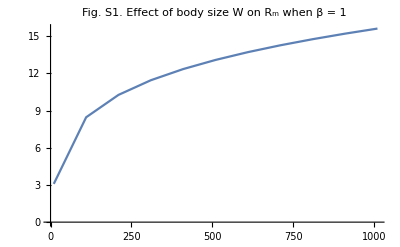
-Graphics-Host mass WGeneralist R_m

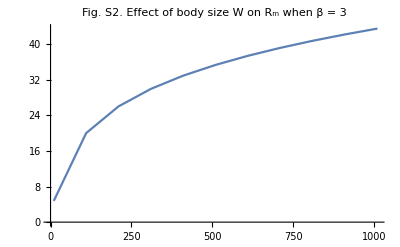
-Graphics-Host mass WGeneralist R_m

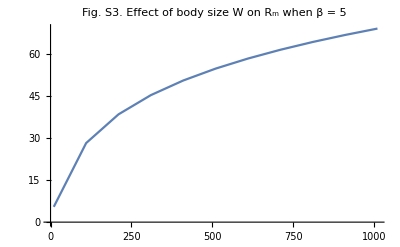
-Graphics-Host mass WGeneralist R_m

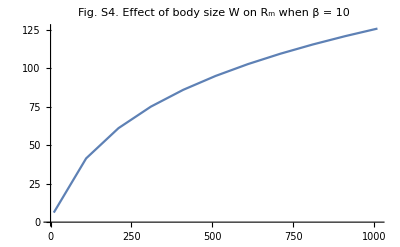
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S1. Effect of body size W on R_m when β = 1"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S2. Effect of body size W on R_m when β = 3"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[5,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S3. Effect of body size W on R_m when β = 5"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[10,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S4. Effect of body size W on R_m when β = 10"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the parasite loss rate from the environment γ.

```mathematica
(* Compute Rm for a range of W and γ values *)
RmAcrossWg=Table[Table[RmV/.{β->1,γ->g,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{g,0.01,1.01,0.1}];
```

Increasing host body size increases R_m, regardless of the value of γ, thereby making it easier for the generalist to invade. This can been seen in Figs. S5-S8 below.

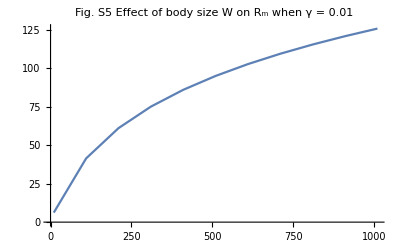
-Graphics-Host mass WGeneralist R_m

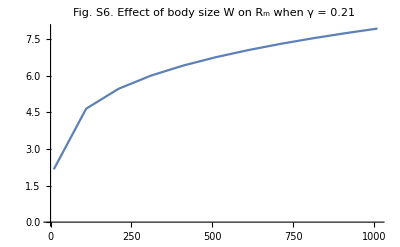
-Graphics-Host mass WGeneralist R_m

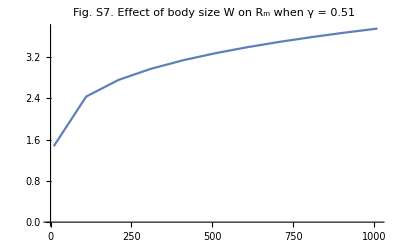
-Graphics-Host mass WGeneralist R_m

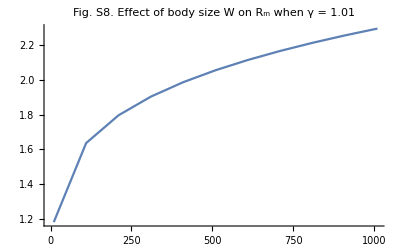
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S5 Effect of body size W on R_m when γ = 0.01"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S6. Effect of body size W on R_m when γ = 0.21"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S7. Effect of body size W on R_m when γ = 0.51"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S8. Effect of body size W on R_m when γ = 1.01"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the temperature T.

```mathematica
(* Compute Rm for a range of W and T values *)
RmAcrossWT=Table[Table[RmV/.{β->1,γ->0.2,W->Wval,T->Tval,a->0.8,f->0.8},{Tval,270,310,2}],{Wval,10,1010,100}];
```

Increasing temperature decreases R_m, regardless of host mass, thus making it more difficult for the generalist endoparasite to invade. This can be seen in Figs. S9-S12 below.

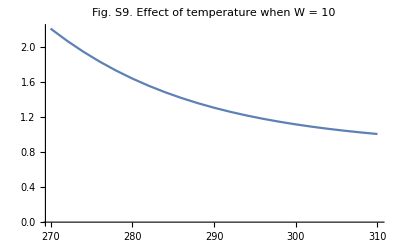
-Graphics-TemperatureGeneralist R_m

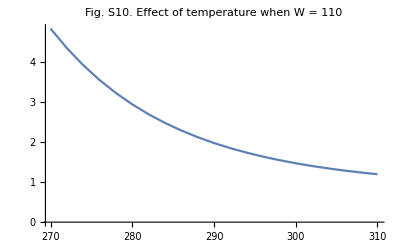
-Graphics-TemperatureGeneralist R_m

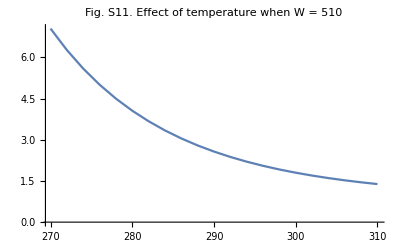
-Graphics-TemperatureGeneralist R_m

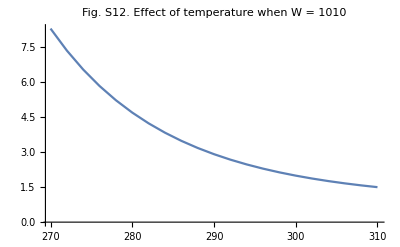
-Graphics-TemperatureGeneralist R_m

```mathematica
Tvals=Table[T,{T,270,310,2}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[1,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S9. Effect of temperature when W = 10"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[2,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S10. Effect of temperature when W = 110"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[6,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S11. Effect of temperature when W = 510"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[11,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S12. Effect of temperature when W = 1010"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

#### Ectoparasites:

The only change from the endoparasite case is with the scaling of λ:

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(5/12),λ2->λ0 Exp[-Ε/(k T)] (f W)^(5/12),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
allompars={Ε->0.43,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

We compute the value of R_m, varying host body size W and the contact rate β.

```mathematica
(* Rm, plugging in the parameter values from Table 1, the equilibria calculated above, the allometric scaling relationships, and the parameters of the allometric functions *)
RmV=Rm/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]/.P1Eq[[2]]/.S2->K2/.{σC1->1,βD1->0,D2ss->0,x1->1/2,I2s->0,P2->0,βS1->β,βI1->β,βS2->β}/.allom/.allompars;
(* Compute Rm for a range of W and β values *)
RmAcrossWB=Table[Table[RmV/.{β->B,γ->0.1,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{B,1,10,1}];
```

The relationship between host body size and R_m depends on the value of β. For very low β, the generalist cannot invade. For values of β large enough to permit the generalist to invade, increasing host body size first increases, then decreases, R_m. Note that this is the same response as was the case for the model without coinfection. This can be seen in Figs. S13-S16 below.

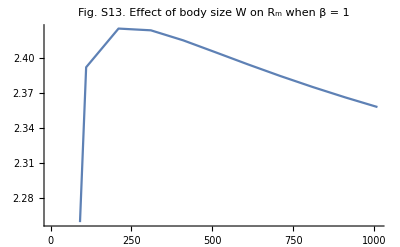
-Graphics-Host mass WGeneralist R_m

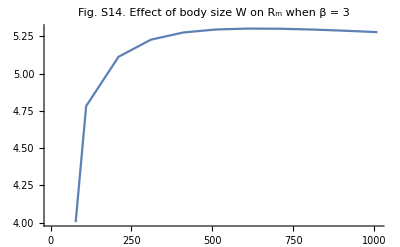
-Graphics-Host mass WGeneralist R_m

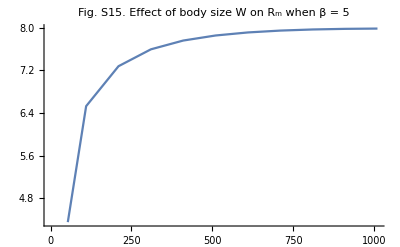
-Graphics-Host mass WGeneralist R_m

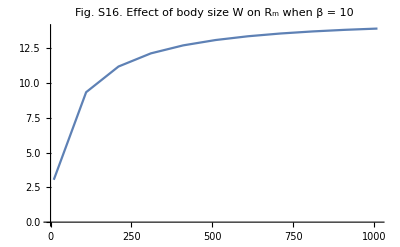
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S13. Effect of body size W on R_m when β = 1"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S14. Effect of body size W on R_m when β = 3"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[5,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S15. Effect of body size W on R_m when β = 5"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[10,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S16. Effect of body size W on R_m when β = 10"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the temperature T to determine the effect of temperature.

```mathematica
(* Compute Rm for a range of W and T values *)
RmAcrossWT=Table[Table[RmV/.{β->0.5,γ->0.1,W->Wval,T->Tval,a->0.8,f->0.8},{Tval,270,310,2}],{Wval,10,1010,100}];
```

Increasing temperature decreases R_m, regardless of host mass, thus making it more difficult for the generalist endoparasite to invade. This can be seen in Figs. S17-S20 below.

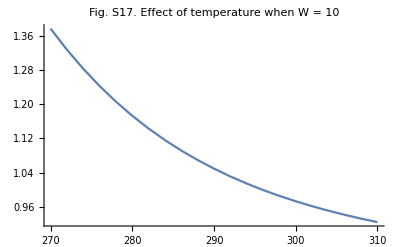
-Graphics-TemperatureGeneralist R_m

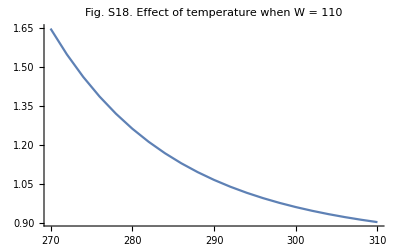
-Graphics-TemperatureGeneralist R_m

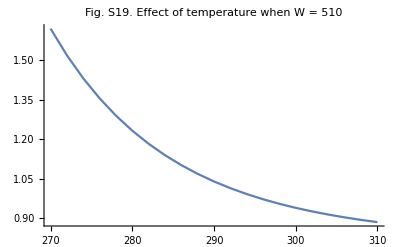
-Graphics-TemperatureGeneralist R_m

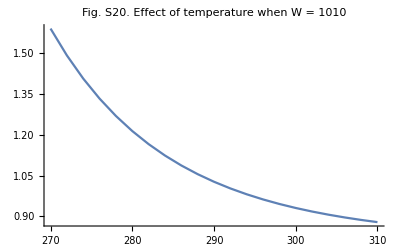
-Graphics-TemperatureGeneralist R_m

```mathematica
Tvals=Table[T,{T,270,310,2}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[1,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S17. Effect of temperature when W = 10"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[2,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S18. Effect of temperature when W = 110"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[6,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S19. Effect of temperature when W = 510"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[11,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S20. Effect of temperature when W = 1010"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

### Case 5: Two specialist parasites, coinfection, parasite regulation of host population size; avoidance of non-susceptible hosts

Based on the parameters presented in Table 1 in the main text, the R_m expression will is nearly identical to Eqn. 12 in the main text: R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+γ) (μ_1/(μ_1+β_I_1 OverHat[P_1]) (a λ_1)/μ_1+(β_I_1 OverHat[P_1])/(μ_1+β_I_1 OverHat[P_1]) (a (1-x_1)λ_1)/μ_1)+(β_I_1 OverHat[I_(1,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+γ)(a (1-x_1)λ_1)/μ_1+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+γ) (μ_2/(μ_2+β_I_2 OverHat[P_2]) (a λ_2)/μ_2+(β_I_2 OverHat[P_2])/(μ_2+β_I_2 OverHat[P_2]) (a (1-x_2)λ_2)/μ_2)+(β_I_2 OverHat[I_(2,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+β_I_2 OverHat[I_(2,s)]+γ)(a (1-x_2)λ_2)/μ_2 >1.

The generalized R_m expression for any number of hosts (Eq. 12 in the main text) follows from this expression.

Based on the parameters presented in Table 1 in the main text, the R_m expression will simplify to the expression R_m=(β_S_1 OverHat[S_1])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ) (μ_1/(μ_1+β_I_1 OverHat[P_1]) (a λ_1)/μ_1+(β_I_1 OverHat[P_1])/(μ_1+β_I_1 OverHat[P_1]) (a (1-x_1)λ_1)/μ_1)+(β_I_1 OverHat[I_(1,s)])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ)(a (1-x_1)λ_1)/μ_1+(β_S_2 OverHat[S_2])/(β_S_1 OverHat[S_1]+β_S_2 OverHat[S_2]+β_I_1 OverHat[I_(1,s)]+γ) ( (a λ_2)/μ_2). 
The parasite can invade if R_m>1. 

Unfortunately, it is analytically intractable to determine the sign of (∂R_m)/(∂W) or (∂R_m)/(∂T), so we use numerical exploration to determine the effect of host body size and environmental temperature on the R_m.

```mathematica
(* Rm at the parameters for this case from Table 1 *)
Rm/.{βD1->0,βD2->0,σC1->1,σC2->1}
```

(a I1s (1-x1) βI1 λ1)/((I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ1)+(S1 βS1 ((a λ1)/(P1 βI1+μ1)+(a P1 (1-x1) βI1 λ1)/(μ1 (P1 βI1+μ1))))/(I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ)+(a I2s (1-x2) βI2 λ2)/((I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ) μ2)+(S2 βS2 ((a λ2)/(P2 βI2+μ2)+(a P2 (1-x2) βI2 λ2)/(μ2 (P2 βI2+μ2))))/(I1s βI1+I2s βI2+S1 βS1+S2 βS2+γ)

#### Endoparasites:

Many of the parameters of the model are set by allometric relationships and have been established previously (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007).

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
allompars={Ε->0.43,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are complex. This excludes parameters related to the costs associated with generalism, including a (the reduction in shedding rate for generalists), σ_C_1 (the probability of coinfection, which we hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection, which we hold constant at 1/2). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing a, reducing σ_C_1, or increasing x_1 will all reduce R_m, making invasion by the generalist more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are the contact rates between hosts and parasites and γ (the loss rate of parasites from the environment). For simplicity, we assume that all contact rates are equal (β_S_1=β_I_1=β_S_2=β).

We can solve for the equilibria analytically, although the expression for OverHat[P_1] and OverHat[P_2]cannot be expressed simply.

```mathematica
(* Solving for Subscript[S, 1] in terms of Subscript[I, 1,s] and Subscript[P, 1]*)
S1Eq=Solve[(dI1sdt/.{σC1->1,σD1->1,Pg->0})==0,S1];
(* Solving for Subscript[I, 1,s] in terms of Subscript[D, 1,s,s] and Subscript[P, 1] *)
I1sEq=Solve[(dD1ssdt/.σD1->1)==0,I1s];
(* Solving for Subscript[D, 1,s,s] in terms of Subscript[P, 1] *)
D1ssEq=Simplify[Solve[(dP1dt/.{βC1->0,βD1->0,C1sg->0}/.S1Eq[[1]]/.I1sEq[[1]])==0,D1ss]]
(* Solving for Subscript[I, 1,s] in terms of Subscript[P, 1] *)
I1sEq=Simplify[I1sEq/.D1ssEq[[1]]]
(* Solving for Subscript[S, 1] in terms of Subscript[P, 1] *)
S1Eq=Simplify[S1Eq/.I1sEq[[1]]]
(* Solving for Subscript[P, 1] *)
P1Eq=Solve[Simplify[dS1dt/.{C1sg->0,I1g->0,Pg->0}/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]]==0,P1];
(* Solving for Subscript[S, 2] in terms of Subscript[I, 2,s] and Subscript[P, 2]*)
S2Eq=Solve[(dI2sdt/.{σC2->1,σD2->1,Pg->0})==0,S2];
(* Solving for Subscript[I, 2,s] in terms of Subscript[D, 2,s,s] and Subscript[P, 2] *)
I2sEq=Solve[(dD2ssdt/.σD2->1)==0,I2s];
(* Solving for Subscript[D, 2,s,s] in terms of Subscript[P, 2] *)
D2ssEq=Simplify[Solve[(dP2dt/.{βC2->0,βD2->0,C2sg->0}/.S2Eq[[1]]/.I2sEq[[1]])==0,D2ss]]
(* Solving for Subscript[I, 2,s] in terms of Subscript[P, 2] *)
I2sEq=Simplify[I2sEq/.D2ssEq[[1]]]
(* Solving for Subscript[S, 2] in terms of Subscript[P, 2] *)
S2Eq=Simplify[S2Eq/.I2sEq[[1]]]
(* Solving for Subscript[P, 2] *)
P2Eq=Solve[Simplify[dS2dt/.{C2sg->0,I2g->0,Pg->0}/.S2Eq[[1]]/.I2sEq[[1]]/.D2ssEq[[1]]]==0,P2];
```

{{D1ss→(P1^2 βI1 γ)/(P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1)}}

{{I1s→(P1 γ μ1)/(P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1)}}

{{S1→(γ μ1 (P1 βI1+μ1))/(βS1 (P1 βI1 (λ1-2 μ1)+(λ1-μ1) μ1))}}

{{D2ss→(P2^2 βI2 γ)/(P2 βI2 (λ2-2 μ2)+(λ2-μ2) μ2)}}

{{I2s→(P2 γ μ2)/(P2 βI2 (λ2-2 μ2)+(λ2-μ2) μ2)}}

{{S2→(γ μ2 (P2 βI2+μ2))/(βS2 (P2 βI2 (λ2-2 μ2)+(λ2-μ2) μ2))}}

With these equilibria, we can compute the value of R_m, varying host body size W and the contact rate β.

```mathematica
(* Rm, plugging in the parameter values from Table 1, the equilibria calculated above, the allometric scaling relationships, and the parameters of the allometric functions *)
RmV=Rm/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]/.P1Eq[[2]]/.S2Eq[[1]]/.I2sEq[[1]]/.D2ssEq[[1]]/.P2Eq[[2]]/.{σC1->1,σC2->1,βD1->0,βD2->0,x1->1/2,x2->1/2,βS1->β,βI1->β,βS2->β,βI2->β}/.allom/.allompars;
(* Compute Rm for a range of W and β values *)
RmAcrossWB=Table[Table[RmV/.{β->B,γ->0.1,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{B,1,10,1}];
```

Increasing host body size increases R_m, regardless of the value of β, thereby making it easier for the generalist to invade. This can be seen in Figs. S21-S24 below.

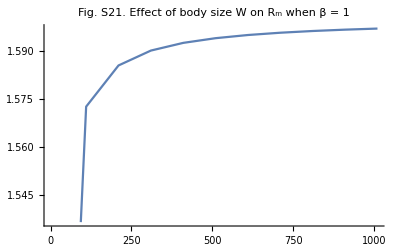
-Graphics-Host mass WGeneralist R_m

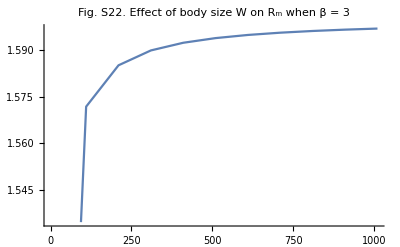
-Graphics-Host mass WGeneralist R_m

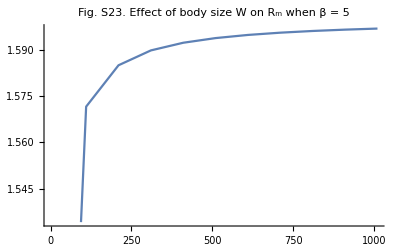
-Graphics-Host mass WGeneralist R_m

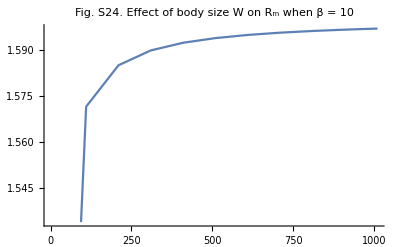
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S21. Effect of body size W on R_m when β = 1"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S22. Effect of body size W on R_m when β = 3"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[5,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S23. Effect of body size W on R_m when β = 5"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[10,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S24. Effect of body size W on R_m when β = 10"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the parasite loss rate from the environment γ.

```mathematica
(* Compute Rm for a range of W and γ values *)
RmAcrossWg=Table[Table[RmV/.{β->1,γ->g,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{g,0.01,1.01,0.1}];
```

Increasing host body size increases R_m, regardless of the value of γ, thereby making it easier for the generalist to invade. This can been seen in Figs. S25-S28 below.

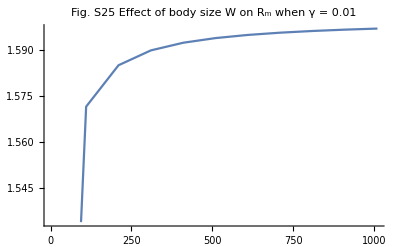
-Graphics-Host mass WGeneralist R_m

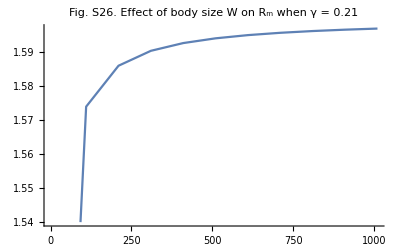
-Graphics-Host mass WGeneralist R_m

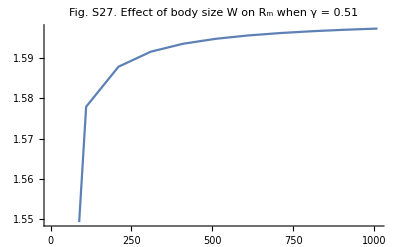
-Graphics-Host mass WGeneralist R_m

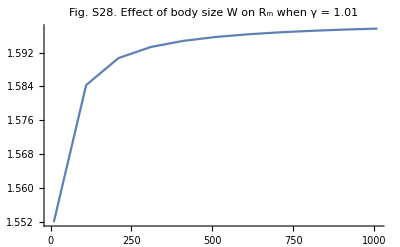
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S25 Effect of body size W on R_m when γ = 0.01"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S26. Effect of body size W on R_m when γ = 0.21"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S27. Effect of body size W on R_m when γ = 0.51"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[11,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S28. Effect of body size W on R_m when γ = 1.01"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the temperature T.

```mathematica
(* Compute Rm for a range of W and T values *)
RmAcrossWT=Table[Table[RmV/.{β->1,γ->0.2,W->Wval,T->Tval,a->0.8,f->0.8},{Tval,270,310,2}],{Wval,10,1010,100}];
```

Increasing temperature increases R_m, although the increase is very slight, and as host mass increases, the increase in R_m with temperature gets shallower. This can be seen in Figs. S29-S32 below.

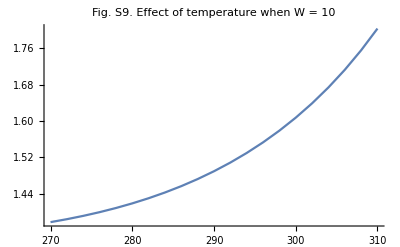
-Graphics-TemperatureGeneralist R_m

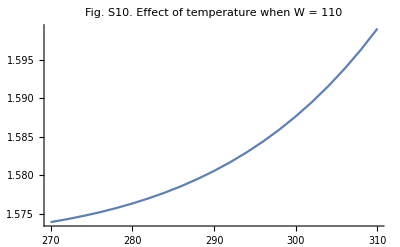
-Graphics-TemperatureGeneralist R_m

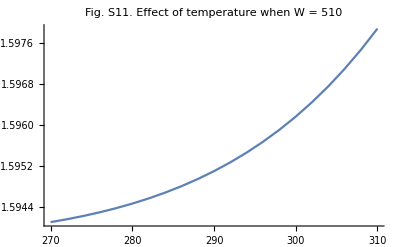
-Graphics-TemperatureGeneralist R_m

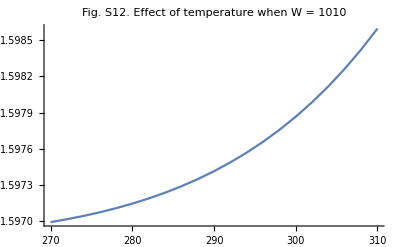
-Graphics-TemperatureGeneralist R_m

```mathematica
Tvals=Table[T,{T,270,310,2}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[1,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S29. Effect of temperature when W = 10"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[2,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S30. Effect of temperature when W = 110"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[6,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S31. Effect of temperature when W = 510"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[11,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S32. Effect of temperature when W = 1010"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

#### Ectoparasites:

All that needs to be changed from the previous case is the scaling of λ with body size.

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(5/12),λ2->λ0 Exp[-Ε/(k T)] (f W)^(5/12),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
allompars={Ε->0.43,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

We can compute the value of R_m, varying host body size W and the contact rate β.

```mathematica
(* Rm, plugging in the parameter values from Table 1, the equilibria calculated above, the allometric scaling relationships, and the parameters of the allometric functions *)
RmV=Rm/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]/.P1Eq[[2]]/.S2Eq[[1]]/.I2sEq[[1]]/.D2ssEq[[1]]/.P2Eq[[2]]/.{σC1->1,σC2->1,βD1->0,βD2->0,x1->1/2,x2->1/2,βS1->β,βI1->β,βS2->β,βI2->β}/.allom/.allompars;
(* Compute Rm for a range of W and β values *)
RmAcrossWB=Table[Table[RmV/.{β->B,γ->0.1,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{B,1,10,1}];
```

Increasing host body size increases R_m, regardless of the value of β, thereby making it easier for the generalist to invade. This can be seen in Figs. S33-S36 below.

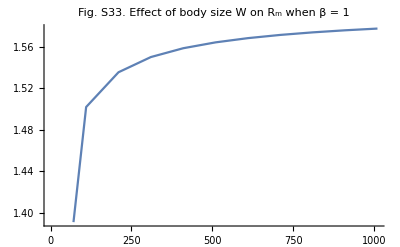
-Graphics-Host mass WGeneralist R_m

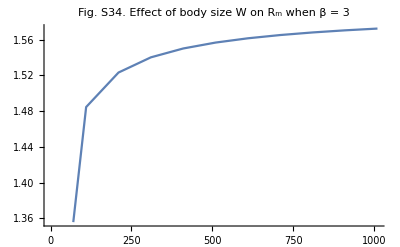
-Graphics-Host mass WGeneralist R_m

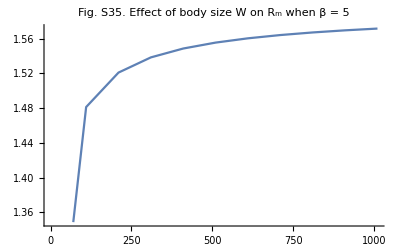
-Graphics-Host mass WGeneralist R_m

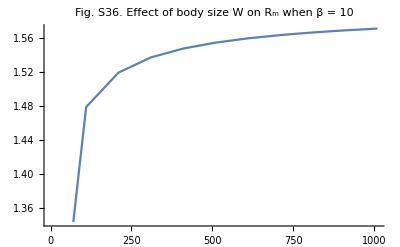
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S33. Effect of body size W on R_m when β = 1"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S34. Effect of body size W on R_m when β = 3"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[5,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S35. Effect of body size W on R_m when β = 5"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWB[[10,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S36. Effect of body size W on R_m when β = 10"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the parasite loss rate from the environment γ.

```mathematica
(* Compute Rm for a range of W and γ values *)
RmAcrossWg=Table[Table[
RmV/.{β->1,γ->g,W->Wval,T->270,a->0.8,f->0.8},{Wval,10,1010,100}],{g,0.01,0.1,0.01}];
```

Increasing host body size increases R_m, regardless of the value of γ, thereby making it easier for the generalist to invade. This can been seen in Figs. S37-S40 below.

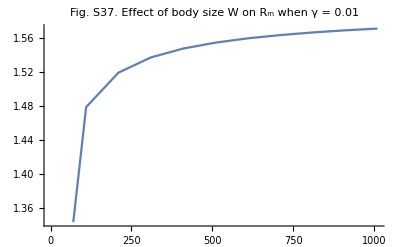
-Graphics-Host mass WGeneralist R_m

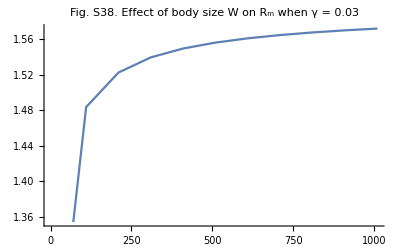
-Graphics-Host mass WGeneralist R_m

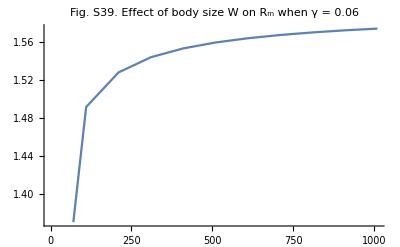
-Graphics-Host mass WGeneralist R_m

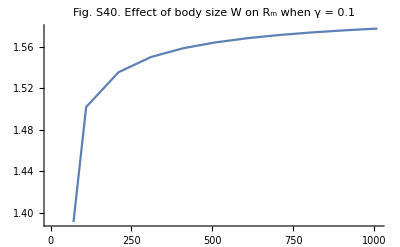
-Graphics-Host mass WGeneralist R_m

```mathematica
Wvals=Table[W,{W,10,1010,100}];
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[1,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S37. Effect of body size W on R_m when γ = 0.01"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[3,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S38. Effect of body size W on R_m when γ = 0.03"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[6,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S39. Effect of body size W on R_m when γ = 0.06"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Wvals[[i]],Re[RmAcrossWg[[10,i]]]},{i,1,Length[Wvals]}],PlotLabel->"Fig. S40. Effect of body size W on R_m when γ = 0.1"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

We can also compute the value of R_m, varying host body size W and the temperature T.

```mathematica
(* Compute Rm for a range of W and T values *)
RmAcrossWT=Table[Table[RmV/.{β->1,γ->0.1,W->Wval,T->Tval,a->0.8,f->0.8},{Tval,270,310,2}],{Wval,10,1010,100}];
```

Increasing temperature increases R_m, making it easier for the generalist to invade. This can be seen in Figs. S41-S44 below.

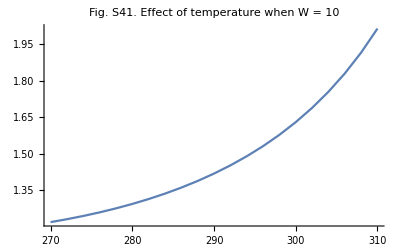
-Graphics-TemperatureGeneralist R_m

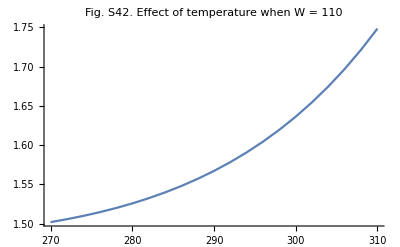
-Graphics-TemperatureGeneralist R_m

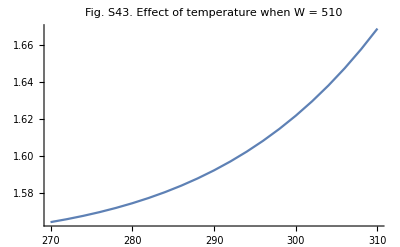
-Graphics-TemperatureGeneralist R_m

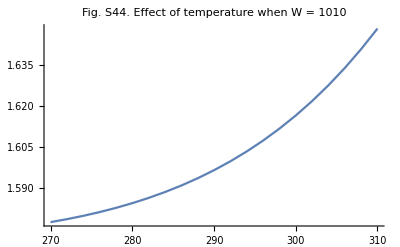
-Graphics-TemperatureGeneralist R_m

```mathematica
Tvals=Table[T,{T,270,310,2}];
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[1,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S41. Effect of temperature when W = 10"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[2,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S42. Effect of temperature when W = 110"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[6,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S43. Effect of temperature when W = 510"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
Labeled[ListLinePlot[Table[{Tvals[[i]],Re[RmAcrossWT[[11,i]]]},{i,1,Length[Tvals]}],PlotLabel->"Fig. S44. Effect of temperature when W = 1010"],{"Temperature","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

### Case 6: Two specialist parasites, coinfection, parasite regulation of host population size; no avoidance of non-susceptible hosts

The R_m expression cannot be simplifed at all from the form presented in Eqn. 12 in the main text. 

However, we can solve for OverHat[S_1], OverHat[I_(1,s)],OverHat[D_(1,s,s)] in terms of OverHat[P_1] and OverHat[S_2], OverHat[I_(2,s)],OverHat[D_(2,s,s)] in terms of OverHat[P_2].

```mathematica
Solve[(dP1dt/.{C1sg->0}/.{S1->(I1s P1 βI1+I1s μ1)/(P1 βS1)}/.{I1s->(D1ss μ1)/(P1 βI1)})==0,D1ss]//Simplify
```

{{D1ss→-((P1^2 βI1 γ)/(P1^2 βD1 βI1-P1 βI1 λ1+2 P1 βI1 μ1-λ1 μ1+μ1^2))}}

```mathematica
(* Solving for Subscript[S, 1] in terms of Subscript[I, 1,s] and Subscript[P, 1]*)
S1Eq=Solve[(dI1sdt/.{σC1->1,σD1->1,Pg->0})==0,S1];
(* Solving for Subscript[I, 1,s] in terms of Subscript[D, 1,s,s] and Subscript[P, 1] *)
I1sEq=Solve[(dD1ssdt/.σD1->1)==0,I1s];
(* Solving for Subscript[D, 1,s,s] in terms of Subscript[P, 1] *)
D1ssEq=Simplify[Solve[(dP1dt/.{C1sg->0}/.S1Eq[[1]]/.I1sEq[[1]])==0,D1ss]]
(* Solving for Subscript[I, 1,s] in terms of Subscript[P, 1] *)
I1sEq=Simplify[I1sEq/.D1ssEq[[1]]]
(* Solving for Subscript[S, 1] in terms of Subscript[P, 1] *)
S1Eq=Simplify[S1Eq/.I1sEq[[1]]]
(* Solving for Subscript[P, 1] *)
P1Eq=Solve[Simplify[dS1dt/.{C1sg->0,I1g->0,Pg->0}/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]]==0,P1];
(* Solving for Subscript[S, 2] in terms of Subscript[I, 2,s] and Subscript[P, 2]*)
S2Eq=Solve[(dI2sdt/.{σC2->1,σD2->1,Pg->0})==0,S2];
(* Solving for Subscript[I, 2,s] in terms of Subscript[D, 2,s,s] and Subscript[P, 2] *)
I2sEq=Solve[(dD2ssdt/.σD2->1)==0,I2s];
(* Solving for Subscript[D, 2,s,s] in terms of Subscript[P, 2] *)
D2ssEq=Simplify[Solve[(dP2dt/.{C2sg->0}/.S2Eq[[1]]/.I2sEq[[1]])==0,D2ss]]
(* Solving for Subscript[I, 2,s] in terms of Subscript[P, 2] *)
I2sEq=Simplify[I2sEq/.D2ssEq[[1]]]
(* Solving for Subscript[S, 2] in terms of Subscript[P, 2] *)
S2Eq=Simplify[S2Eq/.I2sEq[[1]]]
(* Solving for Subscript[P, 2] *)
P2Eq=Solve[Simplify[dS2dt/.{C2sg->0,I2g->0,Pg->0}/.S2Eq[[1]]/.I2sEq[[1]]/.D2ssEq[[1]]]==0,P2];
```

{{D1ss→-((P1^2 βI1 γ)/(P1^2 βD1 βI1-P1 βI1 λ1+2 P1 βI1 μ1-λ1 μ1+μ1^2))}}

{{I1s→-((P1 γ μ1)/(P1^2 βD1 βI1-P1 βI1 λ1+2 P1 βI1 μ1-λ1 μ1+μ1^2))}}

{{S1→-((γ μ1 (P1 βI1+μ1))/(βS1 (P1^2 βD1 βI1-P1 βI1 (λ1-2 μ1)+μ1 (-λ1+μ1))))}}

{{D2ss→-((P2^2 βI2 γ)/(P2^2 βD2 βI2-P2 βI2 λ2+2 P2 βI2 μ2-λ2 μ2+μ2^2))}}

{{I2s→-((P2 γ μ2)/(P2^2 βD2 βI2-P2 βI2 λ2+2 P2 βI2 μ2-λ2 μ2+μ2^2))}}

{{S2→-((γ μ2 (P2 βI2+μ2))/(βS2 (P2^2 βD2 βI2-P2 βI2 (λ2-2 μ2)+μ2 (-λ2+μ2))))}}

If we plug these equilibria into the expression for R_m, we can simplify it considerably, if we also make the assumption that x_1=x_2=0.5, σ_C_1=σ_C_2=1, and β_I_1=β_I_2=β_D_1=β_D_2=β.

```mathematica
(* Simplifying the expression for Subscript[R, m] *)
Simplify[Rm/.S1Eq[[1]]/.I1sEq[[1]]/.D1ssEq[[1]]/.S2Eq[[1]]/.I2sEq[[1]]/.D2ssEq[[1]]/.{x1->1/2,x2->1/2,σC1->1,σC2->1,βI1->β,βI2->β,βD1->β,βD2->β}]
```

(a (P2 β λ1+P1 β λ2-2 λ1 λ2+λ2 μ1+λ1 μ2))/(-λ1 λ2+P1 β (P2 β+μ2)+μ1 (P2 β+μ2))

The generalist can only invade if the numerator is larger than then denominator when a=1. This is only true if (β OverHat[P_1]-λ_1+μ_1)(β OverHat[P_2]-λ_2+μ_2)<0. But both of these expressions must be negative to guarantee the positivity of OverHat[S_1] and OverHat[S_2], which means that the generalist can never invade.

```mathematica
(* Is the numerator ever larger than the denominator? This requires the following to be true *)
Simplify[Expand[(P2 β λ1+P1 β λ2-2 λ1 λ2+λ2 μ1+λ1 μ2)>-λ1 λ2+P1 β (P2 β+μ2)+μ1 (P2 β+μ2)]]
```

(P1 β-λ1+μ1) (P2 β-λ2+μ2)<0

## Derivation of R_m for a model with constant host population size

Here we must derive a new model, since we are no longer assuming that the parasite regulates the host population size. We assume that the population sizes for hosts 1 and 2 are constant at K_1 and K_2, respectively. As such, we do not need to keep track of the dynamics of both susceptible and infected hosts - we can simply track the prevalence of infection. For example, we define I_(1,s) and I_(2,s) as the fraction of the host populations that are singly-infected by the specialist parasites, respectively. 

The dynamics of parasites in the environment are governed by shedding and loss, as before. The rate of shedding depends on the number of infected hosts, e.g., I_(1r)K_1. Similarly, loss due to contact with susceptible hosts depends on the number of susceptible hosts, e.g., (1-I_(1r)-I_(1m))K_1. 

The model is given below:

```mathematica
(* Dynamics of individuals of host species 1 singly infected with its specialist parasite *)
dI1sdt=βS1 (1-I1s-D1ss-I1g-C1sg) P1-σD1 βI1 I1s P1-σC1 βI1 I1s Pg -μ1 I1s;
(* Dynamics of individuals of host species 1 doubly infected with its specialist parasite *)
dD1ssdt=σD1 βI1 I1s P1-μ1 D1ss;
(* Dynamics of the specialist parasite of host species 1 in the environment *)
dP1dt=λ1 (I1s+D1ss+x1 C1sg)K1-(βS1 (1-I1s-D1ss)+βI1 I1s+βD1 D1ss+βI1 I1g+βC1 C1sg)K1 P1-γ P1; 

(* Dynamics of individuals of host species 2 singly infected with its specialist parasite *)
dI2sdt=βS2 (1-I2s-D2ss-I2g-C2sg) P2-σD2 βI2 I2s P2-σC2 βI2 I2s Pg -μ2 I2s;
(* Dynamics of individuals of host species 2 doubly infected with its specialist parasite *)
dD2ssdt=σD2 βI2 I2s P2-μ2 D2ss;
(* Dynamics of the specialist parasite of host species 2 in the environment *)
dP2dt=λ2 (I2s+D2ss+x2 C2sg)K2-(βS2 (1-I2s-D2ss)+βI2 I2s+βD2 D2ss+βI2 I2g+βC2 C2sg) K2 P2-γ P2; 

(* Dynamics of individuals of host species 1 singly infected with the generalist parasite *)
dI1gdt=βS1 (1-I1s-D1ss-I1g-C1sg) Pg-σC1 βI1 I1g P1-μ1 I1g;
(* Dynamics of individuals of host species 2 singly infected with the generalist parasite *)
dI2gdt=βS2 (1-I2s-D2ss-I2g-C2sg) Pg-σC2 βI2 I2g P2-μ2 I2g;
(* Dynamics of individuals of host species 1 coinfected with its specialist and the generalist parasite *)
dC1sgdt=σC1 βI1 (I1s Pg+I1g P1)-μ1 C1sg;
(* Dynamics of individuals of host species 2 coinfected with its specialist and the generalist parasite *)
dC2sgdt=σC2 βI2 (I2s Pg+I2g P2)-μ2 C2sg;
(* Dynamics of the generalist parasite in the environment *)
dPgdt=a λ1 (I1g+(1-x1) C1sg)K1+a λ2 (I2g+(1-x2) C2sg)K2-(βS1 (1-I1s-D1ss)+βI1 I1s+βD1 D1ss)K1 Pg-(βS2 (1-I2s-D2ss)+βI2 I2s+βD2 D2ss)K2 Pg-γ Pg;
```

Whether the generalist parasite can invade will depend on the stability of the equilibrium 
(OverHat[I_(1,s)],OverHat[D_(1,s,s)],OverHat[P_1],OverHat[I_(2,s)],OverHat[D_(2,s,s)],OverHat[P_2],0,0,0,0,0). This can be evaluated by looking at the eigenvalues of the Jacobian matrix for the full system. The Jacobian matrix at this equilibrium has a simple block upper triangular structure: J=(J_1
0
00
J_2
0M_1
M_2
J_m), where J_1 is the submatrix that determines the stability of the (I_(1,s),D_(1,s,s),P_1) subsystem and J_2 is the submatrix that determines the stability of the (I_(2,s),D_(2,s,s),P_2) subsystem. J_m is the submatrix of partial derivatives involving the equations for the generalist. Because of its simple structure, the eigenvalues of the full system are given by the eigenvalues of the submatrices J_1, J_2 and J_m. Assuming that the (I_(1,s),D_(1,s,s),P_1) and  (I_(2,s),D_(2,s,s),P_2) subsystems are both stable, all of the eigenvalues of J_1 and J_2 are negative. Therefore, we are interested only in the eigenvalues of J_m.

```mathematica
(* Calculating the Jacobian matrix and evaluating it at the equilibrium where Subscript[I, 1,g]=Subscript[I, 2,g]=Subscript[C, 1,s,g]=Subscript[C, 2,s,g]=Subscript[P, g]=0 *)
J={{D[dI1sdt,I1s],D[dI1sdt,D1ss],D[dI1sdt,P1],
D[dI1sdt,I2s],D[dI1sdt,D2ss],D[dI1sdt,P2],
D[dI1sdt,I1g],D[dI1sdt,I2g],D[dI1sdt,C1sg],D[dI1sdt,C2sg],D[dI1sdt,Pg]},
{D[dD1ssdt,I1s],D[dD1ssdt,D1ss],D[dD1ssdt,P1],
D[dD1ssdt,I2s],D[dD1ssdt,D2ss],D[dD1ssdt,P2],
D[dD1ssdt,I1g],D[dD1ssdt,I2g],D[dD1ssdt,C1sg],D[dD1ssdt,C2sg],D[dD1ssdt,Pg]},
{D[dP1dt,I1s],D[dP1dt,D1ss],D[dP1dt,P1],
D[dP1dt,I2s],D[dP1dt,D2ss],D[dP1dt,P2],
D[dP1dt,I1g],D[dP1dt,I2g],D[dP1dt,C1sg],D[dP1dt,C2sg],D[dP1dt,Pg]},
{D[dI2sdt,I1s],D[dI2sdt,D1ss],D[dI2sdt,P1],
D[dI2sdt,I2s],D[dI2sdt,D2ss],D[dI2sdt,P2],
D[dI2sdt,I1g],D[dI2sdt,I2g],D[dI2sdt,C1sg],D[dI2sdt,C2sg],D[dI2sdt,Pg]},
{D[dD2ssdt,I1s],D[dD2ssdt,D1ss],D[dD2ssdt,P1],
D[dD2ssdt,I2s],D[dD2ssdt,D2ss],D[dD2ssdt,P2],
D[dD2ssdt,I1g],D[dD2ssdt,I2g],D[dD2ssdt,C1sg],D[dD2ssdt,C2sg],D[dD2ssdt,Pg]},
{D[dP2dt,I1s],D[dP2dt,D1ss],D[dP2dt,P1],
D[dP2dt,I2s],D[dP2dt,D2ss],D[dP2dt,P2],
D[dP2dt,I1g],D[dP2dt,I2g],D[dP2dt,C1sg],D[dP2dt,C2sg],D[dP2dt,Pg]},
{D[dI1gdt,I1s],D[dI1gdt,D1ss],D[dI1gdt,P1],
D[dI1gdt,I2s],D[dI1gdt,D2ss],D[dI1gdt,P2],
D[dI1gdt,I1g],D[dI1gdt,I2g],D[dI1gdt,C1sg],D[dI1gdt,C2sg],D[dI1gdt,Pg]},
{D[dI2gdt,I1s],D[dI2gdt,D1ss],D[dI2gdt,P1],
D[dI2gdt,I2s],D[dI2gdt,D2ss],D[dI2gdt,P2],
D[dI2gdt,I1g],D[dI2gdt,I2g],D[dI2gdt,C1sg],D[dI2gdt,C2sg],D[dI2gdt,Pg]},
{D[dC1sgdt,I1s],D[dC1sgdt,D1ss],D[dC1sgdt,P1],
D[dC1sgdt,I2s],D[dC1sgdt,D2ss],D[dC1sgdt,P2],
D[dC1sgdt,I1g],D[dC1sgdt,I2g],D[dC1sgdt,C1sg],D[dC1sgdt,C2sg],D[dC1sgdt,Pg]},
{D[dC2sgdt,I1s],D[dC2sgdt,D1ss],D[dC2sgdt,P1],
D[dC2sgdt,I2s],D[dC2sgdt,D2ss],D[dC2sgdt,P2],
D[dC2sgdt,I1g],D[dC2sgdt,I2g],D[dC2sgdt,C1sg],D[dC2sgdt,C2sg],D[dC2sgdt,Pg]},
{D[dPgdt,I1s],D[dPgdt,D1ss],D[dPgdt,P1],
D[dPgdt,I2s],D[dPgdt,D2ss],D[dPgdt,P2],
D[dPgdt,I1g],D[dPgdt,I2g],D[dPgdt,C1sg],D[dPgdt,C2sg],D[dPgdt,Pg]}}/.{I1g->0,I2g->0,C1sg->0,C2sg->0,Pg->0};
(* The submatrices *)
(* J1 *)
MatrixForm[J1=J[[1;;3,1;;3]]]
```

(-P1 βS1-μ1-P1 βI1 σD1 | -P1 βS1 | (1-D1ss-I1s) βS1-I1s βI1 σD1
P1 βI1 σD1 | -μ1 | I1s βI1 σD1
-K1 P1 (βI1-βS1)+K1 λ1 | -K1 P1 (βD1-βS1)+K1 λ1 | -K1 (D1ss βD1+I1s βI1+(1-D1ss-I1s) βS1)-γ)

```mathematica
(* J2 *)
MatrixForm[J1=J[[4;;6,4;;6]]]
```

(-P2 βS2-μ2-P2 βI2 σD2 | -P2 βS2 | (1-D2ss-I2s) βS2-I2s βI2 σD2
P2 βI2 σD2 | -μ2 | I2s βI2 σD2
-K2 P2 (βI2-βS2)+K2 λ2 | -K2 P2 (βD2-βS2)+K2 λ2 | -K2 (D2ss βD2+I2s βI2+(1-D2ss-I2s) βS2)-γ)

```mathematica
(* M1 *)
MatrixForm[J1=J[[1;;3,7;;11]]]
```

(-P1 βS1 | 0 | -P1 βS1 | 0 | -I1s βI1 σC1
0 | 0 | 0 | 0 | 0
-K1 P1 βI1 | 0 | -K1 P1 βC1+K1 x1 λ1 | 0 | 0)

```mathematica
(* M12*)
MatrixForm[J1=J[[4;;6,7;;11]]]
```

(0 | -P2 βS2 | 0 | -P2 βS2 | -I2s βI2 σC2
0 | 0 | 0 | 0 | 0
0 | -K2 P2 βI2 | 0 | -K2 P2 βC2+K2 x2 λ2 | 0)

```mathematica
(* Jm *)
```

```mathematica
MatrixForm[Jm=J[[7;;11,7;;11]]]
```

(-μ1-P1 βI1 σC1 | 0 | 0 | 0 | (1-D1ss-I1s) βS1
0 | -μ2-P2 βI2 σC2 | 0 | 0 | (1-D2ss-I2s) βS2
P1 βI1 σC1 | 0 | -μ1 | 0 | I1s βI1 σC1
0 | P2 βI2 σC2 | 0 | -μ2 | I2s βI2 σC2
a K1 λ1 | a K2 λ2 | a K1 (1-x1) λ1 | a K2 (1-x2) λ2 | -K1 (D1ss βD1+I1s βI1+(1-D1ss-I1s) βS1)-K2 (D2ss βD2+I2s βI2+(1-D2ss-I2s) βS2)-γ)

The submatrix J_m=(-μ_1-σ_C_1 β_I_1 OverHat[P_1] | 0 | 0 | 0 | β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])
0 | -μ_2-σ_C_2 β_I_2 OverHat[P_2] | 0 | 0 | β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])
σ_C_1 β_I_1 OverHat[P_1] | 0 | -μ_1 | 0 | σ_C_1 β_I_1 OverHat[I_(1,s)]
0 | σ_C_2 β_I_2 OverHat[P_2] | 0 | -μ_2 | σ_C_2 β_I_2 OverHat[I_(2,s)]
a λ_1 K_1 | a λ_2 K_2 | a (1-x_1) λ_1 K_1 | a (1-x_2) λ_2 K_2 | -(β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])+β_I_1 OverHat[I_(1,s)]+β_D_1 OverHat[D_(1,s,s)])K_1-(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])+β_I_2 OverHat[I_(2,s)]+β_D_2 OverHat[D_(2,s,s)])K_2-γ).
Rather than finding for the eigenvalues of this submatrix, we make use of the Next Generation Theorem and rewrite J_m as F-V, where F=(0 | 0 | 0 | 0 | β_S_2(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])
0 | 0 | 0 | 0 | β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])
σ_C_1 β_I_1 OverHat[P_1] | 0 | 0 | 0 | σ_C_1 β_I_1 OverHat[I_(1,s)]
0 | σ_C_2 β_I_2 OverHat[P_2] | 0 | 0 | σ_C_2 β_I_2 OverHat[I_(2,s)]
0 | 0 | 0 | 0 | 0) and V=(μ_1+σ_C_1 β_I_1 OverHat[P_1] | 0 | 0 | 0 | 0
0 | μ_2+σ_C_2 β_I_2 OverHat[P_2] | 0 | 0 | 0
0 | 0 | μ1 | 0 | 0
0 | 0 | 0 | μ2 | 0
-a λ_1 K_1 | -a λ_2 K_2 | -a (1-x_1) λ_1 K_1 | -a (1-x_2) λ_2 K_2 | (β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])+β_I_1 OverHat[I_(1,s)]+β_D_1 OverHat[D_(1,s,s)])K_1+(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])+β_I_2 OverHat[I_(2,s)]+β_D_2 OverHat[D_(2,s,s)])K_2+γ)

```mathematica
F={{0,0,0,0,(1-I1s-D1ss) βS1},{0,0,0,0,(1-I2s-D2ss) βS2},{P1 βI1 σC1,0,0,0,I1s βI1 σC1},{0,P2 βI2 σC2,0,0,I2s βI2 σC2},{0,0,0,0,0}};
V={{μ1+P1 βI1 σC1,0,0,0,0},{0,μ2+P2 βI2 σC2,0,0,0},{0,0,μ1,0,0},{0,0,0,μ2,0},{-a λ1 K1,-a λ2 K2,-a (1-x1) λ1 K1,-a (1-x2) λ2 K2,((1-I1s-D1ss)  βS1+I1s βI1+D1ss βD1) K1+(D2ss βD2+I2s βI2+(1-I2s-D2ss) βS2) K2+γ}};
Jm==F-V//Simplify
```

True

The Next Generation Theorem states that, if a matrix J can be written J=F-V, where F≥0, V^-1≥ 0 and all of the eigenvalues of -V are negative, then the dominant eigenvalue of J will be greater than zero whenever the spectral radius of F.V^-1>1. Note that the spectral radius largest real part of all of the eigenvalues.

```mathematica
(* Verifying that all elements of V^-1≥0*)
Inverse[V]//Simplify
```

{{1/(μ1+P1 βI1 σC1),0,0,0,0},{0,1/(μ2+P2 βI2 σC2),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(a K1 λ1)/((I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) (μ1+P1 βI1 σC1)),(a K2 λ2)/((I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) (μ2+P2 βI2 σC2)),(a K1 (1-x1) λ1)/((K1 (D1ss (βD1-βS1)+I1s (βI1-βS1)+βS1)+K2 (D2ss (βD2-βS2)+I2s (βI2-βS2)+βS2)+γ) μ1),(a K2 (1-x2) λ2)/((K1 (D1ss (βD1-βS1)+I1s (βI1-βS1)+βS1)+K2 (D2ss (βD2-βS2)+I2s (βI2-βS2)+βS2)+γ) μ2),1/(K1 (D1ss (βD1-βS1)+I1s (βI1-βS1)+βS1)+K2 (D2ss (βD2-βS2)+I2s (βI2-βS2)+βS2)+γ)}}

```mathematica
(* Verifying that all eigenvalues of -V<0 *)
Eigenvalues[-V]//Simplify
```

{-K1 (D1ss (βD1-βS1)+I1s (βI1-βS1)+βS1)-K2 (D2ss (βD2-βS2)+I2s (βI2-βS2)+βS2)-γ,-μ1,-μ2,-μ1-P1 βI1 σC1,-μ2-P2 βI2 σC2}

```mathematica
(* Eigenvalues of F.V^-1 *)
```

```mathematica
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,0,0,-((-a K2 βS2 λ2 μ1^2 μ2+a D2ss K2 βS2 λ2 μ1^2 μ2+a I2s K2 βS2 λ2 μ1^2 μ2-a K1 βS1 λ1 μ1 μ2^2+a D1ss K1 βS1 λ1 μ1 μ2^2+a I1s K1 βS1 λ1 μ1 μ2^2-a K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a D2ss K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a I2s K2 P1 βI1 βS2 λ2 μ1 μ2 σC1-a I1s K1 βI1 λ1 μ1 μ2^2 σC1+a I1s K1 x1 βI1 λ1 μ1 μ2^2 σC1-a I1s K1 P1 βI1^2 λ1 μ2^2 σC1^2+a I1s K1 P1 x1 βI1^2 λ1 μ2^2 σC1^2-a K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a D1ss K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a I1s K1 P2 βI2 βS1 λ1 μ1 μ2 σC2-a I2s K2 βI2 λ2 μ1^2 μ2 σC2+a I2s K2 x2 βI2 λ2 μ1^2 μ2 σC2-a I1s K1 P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I1s K1 P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I2s K2 P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I2s K2 P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I1s K1 P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I1s K1 P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I2s K2 P2 βI2^2 λ2 μ1^2 σC2^2+a I2s K2 P2 x2 βI2^2 λ2 μ1^2 σC2^2-a I2s K2 P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2+a I2s K2 P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-√(a (4 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) ((-1+D2ss+I2s) K2 P2 (-1+x2) βI2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) σC2+(-1+D1ss+I1s) K1 P1 (-1+x1) βI1 βS1 λ1 μ2 σC1 (μ2+P2 βI2 σC2))+a (K1 λ1 μ2 ((-1+D1ss+I1s) βS1 μ1+I1s (-1+x1) βI1 σC1 (μ1+P1 βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) ((-1+D2ss+I2s) βS2 μ2+I2s (-1+x2) βI2 σC2 (μ2+P2 βI2 σC2)))^2)))/(2 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))),-((-a K2 βS2 λ2 μ1^2 μ2+a D2ss K2 βS2 λ2 μ1^2 μ2+a I2s K2 βS2 λ2 μ1^2 μ2-a K1 βS1 λ1 μ1 μ2^2+a D1ss K1 βS1 λ1 μ1 μ2^2+a I1s K1 βS1 λ1 μ1 μ2^2-a K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a D2ss K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a I2s K2 P1 βI1 βS2 λ2 μ1 μ2 σC1-a I1s K1 βI1 λ1 μ1 μ2^2 σC1+a I1s K1 x1 βI1 λ1 μ1 μ2^2 σC1-a I1s K1 P1 βI1^2 λ1 μ2^2 σC1^2+a I1s K1 P1 x1 βI1^2 λ1 μ2^2 σC1^2-a K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a D1ss K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a I1s K1 P2 βI2 βS1 λ1 μ1 μ2 σC2-a I2s K2 βI2 λ2 μ1^2 μ2 σC2+a I2s K2 x2 βI2 λ2 μ1^2 μ2 σC2-a I1s K1 P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I1s K1 P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I2s K2 P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I2s K2 P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I1s K1 P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I1s K1 P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I2s K2 P2 βI2^2 λ2 μ1^2 σC2^2+a I2s K2 P2 x2 βI2^2 λ2 μ1^2 σC2^2-a I2s K2 P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2+a I2s K2 P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2+√(a (4 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) ((-1+D2ss+I2s) K2 P2 (-1+x2) βI2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) σC2+(-1+D1ss+I1s) K1 P1 (-1+x1) βI1 βS1 λ1 μ2 σC1 (μ2+P2 βI2 σC2))+a (K1 λ1 μ2 ((-1+D1ss+I1s) βS1 μ1+I1s (-1+x1) βI1 σC1 (μ1+P1 βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) ((-1+D2ss+I2s) βS2 μ2+I2s (-1+x2) βI2 σC2 (μ2+P2 βI2 σC2)))^2)))/(2 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)))}

The spectral bound condition is
 R_m=(β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])/((β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])+β_I_1 OverHat[I_(1,s)]+β_D_1 OverHat[D_(1,s,s)])K_1+(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])+β_I_2 OverHat[I_(2,s)]+β_D_2 OverHat[D_(2,s,s)])K_2+γ)) (μ_1/(μ_1+σ_C_1 β_I_1 OverHat[P_1]) (a λ_1 K_1)/μ_1+(σ_C_1 β_I_1 OverHat[P_1])/(μ_1+σ_C_1 β_I_1 OverHat[P_1]) (a (1-x_1)λ_1 K_1)/μ_1)+((β_I_1 OverHat[I_(1,s)])/((β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])+β_I_1 OverHat[I_(1,s)]+β_D_1 OverHat[D_(1,s,s)])K_1+(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])+β_I_2 OverHat[I_(2,s)]+β_D_2 OverHat[D_(2,s,s)])K_2+γ))(a (1-x_1)λ_1 K_1)/μ_1+(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])/((β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])+β_I_1 OverHat[I_(1,s)]+β_D_1 OverHat[D_(1,s,s)])K_1+(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])+β_I_2 OverHat[I_(2,s)]+β_D_2 OverHat[D_(2,s,s)])K_2+γ)) (μ_2/(μ_2+σ_C_2 β_I_2 OverHat[P_2]) (a λ_2 K_2)/μ_2+(σ_C_2 β_I_2 OverHat[P_2])/(μ_2+σ_C_2 β_I_2 OverHat[P_2]) (a (1-x_2)λ_2 K_2)/μ_2)+((β_I_2 OverHat[I_(2,s)])/((β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])+β_I_1 OverHat[I_(1,s)]+β_D_1 OverHat[D_(1,s,s)])K_1+(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])+β_I_2 OverHat[I_(2,s)]+β_D_2 OverHat[D_(2,s,s)])K_2+γ))(a (1-x_2)λ_2 K_2)/μ_2 >1.

This expression has the same biological interpretation as Eq. (12) in the main text.

```mathematica
(* The condition for instability of the generalist-free equilibrium is that the spectral bound > 1 *)
-((-a K2 βS2 λ2 μ1^2 μ2+a D2ss K2 βS2 λ2 μ1^2 μ2+a I2s K2 βS2 λ2 μ1^2 μ2-a K1 βS1 λ1 μ1 μ2^2+a D1ss K1 βS1 λ1 μ1 μ2^2+a I1s K1 βS1 λ1 μ1 μ2^2-a K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a D2ss K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a I2s K2 P1 βI1 βS2 λ2 μ1 μ2 σC1-a I1s K1 βI1 λ1 μ1 μ2^2 σC1+a I1s K1 x1 βI1 λ1 μ1 μ2^2 σC1-a I1s K1 P1 βI1^2 λ1 μ2^2 σC1^2+a I1s K1 P1 x1 βI1^2 λ1 μ2^2 σC1^2-a K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a D1ss K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a I1s K1 P2 βI2 βS1 λ1 μ1 μ2 σC2-a I2s K2 βI2 λ2 μ1^2 μ2 σC2+a I2s K2 x2 βI2 λ2 μ1^2 μ2 σC2-a I1s K1 P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I1s K1 P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I2s K2 P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I2s K2 P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I1s K1 P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I1s K1 P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I2s K2 P2 βI2^2 λ2 μ1^2 σC2^2+a I2s K2 P2 x2 βI2^2 λ2 μ1^2 σC2^2-a I2s K2 P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2+a I2s K2 P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-√(a (4 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) ((-1+D2ss+I2s) K2 P2 (-1+x2) βI2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) σC2+(-1+D1ss+I1s) K1 P1 (-1+x1) βI1 βS1 λ1 μ2 σC1 (μ2+P2 βI2 σC2))+a (K1 λ1 μ2 ((-1+D1ss+I1s) βS1 μ1+I1s (-1+x1) βI1 σC1 (μ1+P1 βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) ((-1+D2ss+I2s) βS2 μ2+I2s (-1+x2) βI2 σC2 (μ2+P2 βI2 σC2)))^2)))/(2 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)))>1;
(* Cross-multiplying *)
-((-a K2 βS2 λ2 μ1^2 μ2+a D2ss K2 βS2 λ2 μ1^2 μ2+a I2s K2 βS2 λ2 μ1^2 μ2-a K1 βS1 λ1 μ1 μ2^2+a D1ss K1 βS1 λ1 μ1 μ2^2+a I1s K1 βS1 λ1 μ1 μ2^2-a K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a D2ss K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a I2s K2 P1 βI1 βS2 λ2 μ1 μ2 σC1-a I1s K1 βI1 λ1 μ1 μ2^2 σC1+a I1s K1 x1 βI1 λ1 μ1 μ2^2 σC1-a I1s K1 P1 βI1^2 λ1 μ2^2 σC1^2+a I1s K1 P1 x1 βI1^2 λ1 μ2^2 σC1^2-a K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a D1ss K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a I1s K1 P2 βI2 βS1 λ1 μ1 μ2 σC2-a I2s K2 βI2 λ2 μ1^2 μ2 σC2+a I2s K2 x2 βI2 λ2 μ1^2 μ2 σC2-a I1s K1 P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I1s K1 P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I2s K2 P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I2s K2 P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I1s K1 P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I1s K1 P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I2s K2 P2 βI2^2 λ2 μ1^2 σC2^2+a I2s K2 P2 x2 βI2^2 λ2 μ1^2 σC2^2-a I2s K2 P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2+a I2s K2 P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2-√(a (4 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) ((-1+D2ss+I2s) K2 P2 (-1+x2) βI2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) σC2+(-1+D1ss+I1s) K1 P1 (-1+x1) βI1 βS1 λ1 μ2 σC1 (μ2+P2 βI2 σC2))+a (K1 λ1 μ2 ((-1+D1ss+I1s) βS1 μ1+I1s (-1+x1) βI1 σC1 (μ1+P1 βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) ((-1+D2ss+I2s) βS2 μ2+I2s (-1+x2) βI2 σC2 (μ2+P2 βI2 σC2)))^2))))>(2 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2));

(* Isolating the square root term *)
-√(a (4 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) ((-1+D2ss+I2s) K2 P2 (-1+x2) βI2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) σC2+(-1+D1ss+I1s) K1 P1 (-1+x1) βI1 βS1 λ1 μ2 σC1 (μ2+P2 βI2 σC2))+a (K1 λ1 μ2 ((-1+D1ss+I1s) βS1 μ1+I1s (-1+x1) βI1 σC1 (μ1+P1 βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) ((-1+D2ss+I2s) βS2 μ2+I2s (-1+x2) βI2 σC2 (μ2+P2 βI2 σC2)))^2))>(2 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))-(-((-a K2 βS2 λ2 μ1^2 μ2+a D2ss K2 βS2 λ2 μ1^2 μ2+a I2s K2 βS2 λ2 μ1^2 μ2-a K1 βS1 λ1 μ1 μ2^2+a D1ss K1 βS1 λ1 μ1 μ2^2+a I1s K1 βS1 λ1 μ1 μ2^2-a K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a D2ss K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a I2s K2 P1 βI1 βS2 λ2 μ1 μ2 σC1-a I1s K1 βI1 λ1 μ1 μ2^2 σC1+a I1s K1 x1 βI1 λ1 μ1 μ2^2 σC1-a I1s K1 P1 βI1^2 λ1 μ2^2 σC1^2+a I1s K1 P1 x1 βI1^2 λ1 μ2^2 σC1^2-a K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a D1ss K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a I1s K1 P2 βI2 βS1 λ1 μ1 μ2 σC2-a I2s K2 βI2 λ2 μ1^2 μ2 σC2+a I2s K2 x2 βI2 λ2 μ1^2 μ2 σC2-a I1s K1 P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I1s K1 P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I2s K2 P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I2s K2 P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I1s K1 P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I1s K1 P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I2s K2 P2 βI2^2 λ2 μ1^2 σC2^2+a I2s K2 P2 x2 βI2^2 λ2 μ1^2 σC2^2-a I2s K2 P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2+a I2s K2 P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2)));

(* Squaring both sides and simplifying, the condition becomes: *)
(-√(a (4 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) ((-1+D2ss+I2s) K2 P2 (-1+x2) βI2 βS2 λ2 μ1 (μ1+P1 βI1 σC1) σC2+(-1+D1ss+I1s) K1 P1 (-1+x1) βI1 βS1 λ1 μ2 σC1 (μ2+P2 βI2 σC2))+a (K1 λ1 μ2 ((-1+D1ss+I1s) βS1 μ1+I1s (-1+x1) βI1 σC1 (μ1+P1 βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) ((-1+D2ss+I2s) βS2 μ2+I2s (-1+x2) βI2 σC2 (μ2+P2 βI2 σC2)))^2)))^2>((2 (I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2))-(-((-a K2 βS2 λ2 μ1^2 μ2+a D2ss K2 βS2 λ2 μ1^2 μ2+a I2s K2 βS2 λ2 μ1^2 μ2-a K1 βS1 λ1 μ1 μ2^2+a D1ss K1 βS1 λ1 μ1 μ2^2+a I1s K1 βS1 λ1 μ1 μ2^2-a K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a D2ss K2 P1 βI1 βS2 λ2 μ1 μ2 σC1+a I2s K2 P1 βI1 βS2 λ2 μ1 μ2 σC1-a I1s K1 βI1 λ1 μ1 μ2^2 σC1+a I1s K1 x1 βI1 λ1 μ1 μ2^2 σC1-a I1s K1 P1 βI1^2 λ1 μ2^2 σC1^2+a I1s K1 P1 x1 βI1^2 λ1 μ2^2 σC1^2-a K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a D1ss K1 P2 βI2 βS1 λ1 μ1 μ2 σC2+a I1s K1 P2 βI2 βS1 λ1 μ1 μ2 σC2-a I2s K2 βI2 λ2 μ1^2 μ2 σC2+a I2s K2 x2 βI2 λ2 μ1^2 μ2 σC2-a I1s K1 P2 βI1 βI2 λ1 μ1 μ2 σC1 σC2+a I1s K1 P2 x1 βI1 βI2 λ1 μ1 μ2 σC1 σC2-a I2s K2 P1 βI1 βI2 λ2 μ1 μ2 σC1 σC2+a I2s K2 P1 x2 βI1 βI2 λ2 μ1 μ2 σC1 σC2-a I1s K1 P1 P2 βI1^2 βI2 λ1 μ2 σC1^2 σC2+a I1s K1 P1 P2 x1 βI1^2 βI2 λ1 μ2 σC1^2 σC2-a I2s K2 P2 βI2^2 λ2 μ1^2 σC2^2+a I2s K2 P2 x2 βI2^2 λ2 μ1^2 σC2^2-a I2s K2 P1 P2 βI1 βI2^2 λ2 μ1 σC1 σC2^2+a I2s K2 P1 P2 x2 βI1 βI2^2 λ2 μ1 σC1 σC2^2))))^2//Simplify
```

(I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2) ((I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)+a (K1 λ1 μ2 (I1s (-1+x1) βI1 σC1 (μ1+P1 βI1 σC1)+(-1+D1ss+I1s) βS1 (μ1-P1 (-1+x1) βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) (I2s (-1+x2) βI2 σC2 (μ2+P2 βI2 σC2)+(-1+D2ss+I2s) βS2 (μ2-P2 (-1+x2) βI2 σC2))))<0

```mathematica
(* Dividing the positive coefficient, the condition becomes *)
((I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)+a (K1 λ1 μ2 (I1s (-1+x1) βI1 σC1 (μ1+P1 βI1 σC1)+(-1+D1ss+I1s) βS1 (μ1-P1 (-1+x1) βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) (I2s (-1+x2) βI2 σC2 (μ2+P2 βI2 σC2)+(-1+D2ss+I2s) βS2 (μ2-P2 (-1+x2) βI2 σC2))))<0; 
(* Simplifying, the condition becomes *)
(I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)<(a (K1 λ1 μ2 (I1s (1-x1) βI1 σC1 (μ1+P1 βI1 σC1)+(1-D1ss-I1s) βS1 (μ1+P1 (1-x1) βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) (I2s (1-x2) βI2 σC2 (μ2+P2 βI2 σC2)+(1-D2ss-I2s) βS2 (μ2+P2 (1-x2) βI2 σC2))));

(* Dividing through, the condition becomes *)
(1/((I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)))(a (K1 λ1 μ2 (I1s (1-x1) βI1 σC1 (μ1+P1 βI1 σC1)+(1-D1ss-I1s) βS1 (μ1+P1 (1-x1) βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) (I2s (1-x2) βI2 σC2 (μ2+P2 βI2 σC2)+(1-D2ss-I2s) βS2 (μ2+P2 (1-x2) βI2 σC2))))>1;
(* This expression is equivalent to *)
Rm=(((1-I1s-D1ss) βS1)/(((1-I1s-D1ss) βS1+I1s βI1+D1ss βD1) K1+((1-I2s-D2ss) βS2+I2s βI2+D2ss βD2) K2+γ) ) (μ1/(μ1+P1 βI1 σC1) (a λ1 K1)/μ1+(P1 βI1 σC1)/(μ1+P1 βI1 σC1) (a (1-x1) λ1 K1)/μ1)+((I1s βI1 σC1)/(((1-I1s-D1ss) βS1+I1s βI1+D1ss βD1) K1+((1-I2s-D2ss) βS2+I2s βI2+D2ss βD2) K2+γ)) (a (1-x1) λ1 K1)/μ1+(((1-I2s-D2ss) βS2)/(((1-I1s-D1ss) βS1+I1s βI1+D1ss βD1) K1+((1-I2s-D2ss) βS2+I2s βI2+D2ss βD2) K2+γ) ) (μ2/(μ2+P2 βI2 σC2) (a λ2 K2)/μ2+(P2 βI2 σC2)/(μ2+P2 βI2 σC2) (a (1-x2) λ2 K2)/μ2)+((I2s βI2 σC2)/(((1-I1s-D1ss) βS1+I1s βI1+D1ss βD1) K1+((1-I2s-D2ss) βS2+I2s βI2+D2ss βD2) K2+γ) ) (a (1-x2) λ2 K2)/μ2;
Rm==
(1/((I1s K1 βI1+I2s K2 βI2+D1ss K1 (βD1-βS1)+K1 βS1-I1s K1 βS1+D2ss K2 (βD2-βS2)+K2 βS2-I2s K2 βS2+γ) μ1 μ2 (μ1+P1 βI1 σC1) (μ2+P2 βI2 σC2)))(a (K1 λ1 μ2 (I1s (1-x1) βI1 σC1 (μ1+P1 βI1 σC1)+(1-D1ss-I1s) βS1 (μ1+P1 (1-x1) βI1 σC1)) (μ2+P2 βI2 σC2)+K2 λ2 μ1 (μ1+P1 βI1 σC1) (I2s (1-x2) βI2 σC2 (μ2+P2 βI2 σC2)+(1-D2ss-I2s) βS2 (μ2+P2 (1-x2) βI2 σC2))))//Simplify
```

True

## Calculating the response of R_m for Cases 7-10 in Table 2

### Case 7: Two specialist parasites; no coinfection, constant host population size; avoidance of non-susceptible hosts

Using the R_m expression calculated above, to create this scenario we let β_I_1=β_I_2=β_C_1=β_C_2=β_D_1=β_D_2=0 and D_(1,s,s)=D_(2,s,s)=0. In this case, R_m simplifes to 
R_m=(β_S_1(1-OverHat[I_(1,s)]))/(β_S_1(1-OverHat[I_(1,s)])K_1+β_S_2(1-OverHat[I_(2,s)])K_2+γ) ( (a λ_1 K_1)/μ_1)+(β_S_2(1-OverHat[I_(2,s)]))/(β_S_1(1-OverHat[I_(1,s)])K_1+β_S_2(1-OverHat[I_(2,s)])K_2+γ) ((a λ_2 K_2)/μ_2) >1.

```mathematica
Rm/.{βI1->0,βI2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0}
```

(a (1-I1s) K1 βS1 λ1)/(((1-I1s) K1 βS1+(1-I2s) K2 βS2+γ) μ1)+(a (1-I2s) K2 βS2 λ2)/(((1-I1s) K1 βS1+(1-I2s) K2 βS2+γ) μ2)

In the absence of the generalist parasite, the equilibrium prevalences of infection are I_(1,r)= 1 -(γ μ_1)/(β_S_1 K_1(λ_1-μ_1)) and I_(2,r)= 1-(γ μ_2)/(β_S_2 K_2(λ_2-μ_2)), implying that the equilibrium number of susceptibles are (γ μ_1)/(β_S_1 K_1(λ_1-μ_1)) and (γ μ_2)/(β_S_2 K_2(λ_2-μ_2)).

```mathematica
(* Solving for the equilibria of the Subscript[I, 1,s]-Subscript[P, 1] system *)
Solve[{(dI1sdt/.{C1sg->0,D1ss->0,I1g->0}/.{βI1->0,βI2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0})==0,
(dP1dt/.{C1sg->0,D1ss->0,I1g->0}/.{βI1->0,βI2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0})==0},{I1s,P1}]
(* Solving for the equilibria of the Subscript[I, 2,s]-Subscript[P, 2] system *)
Solve[{(dI2sdt/.{C2sg->0,D2ss->0,I2g->0}/.{βI2->0,βI2->0,βC2->0,βC2->0,βD2->0,βD2->0,D2ss->0,D2ss->0})==0,
(dP2dt/.{C2sg->0,D2ss->0,I2g->0}/.{βI1->0,βI2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0})==0},{I2s,P2}]
```

{{I1s→0,P1→0},{I1s→(K1 βS1 λ1-K1 βS1 μ1-γ μ1)/(K1 βS1 (λ1-μ1)),P1→(K1 βS1 λ1-K1 βS1 μ1-γ μ1)/(βS1 γ)}}

{{I2s→0,P2→0},{I2s→(K2 βS2 λ2-K2 βS2 μ2-γ μ2)/(K2 βS2 (λ2-μ2)),P2→(K2 βS2 λ2-K2 βS2 μ2-γ μ2)/(βS2 γ)}}

We can plug these equilibria into the R_m expression and arrive at a very simple expression for R_m=(a (2 λ_1 λ_2-λ_2 μ_1-λ_1 μ_2))/(λ_1 λ_2-μ_1 μ_2).

```mathematica
(* Plug equilibria into Subscript[R, m] and simplify *)
Rm2=Rm/.{βI1->0,βI2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0}/.{I1s->(K1 βS1 λ1-K1 βS1 μ1-γ μ1)/(K1 βS1 (λ1-μ1)),I2s->(K2 βS2 λ2-K2 βS2 μ2-γ μ2)/(K2 βS2 (λ2-μ2))}//Simplify
```

(a (2 λ1 λ2-λ2 μ1-λ1 μ2))/(λ1 λ2-μ1 μ2)

We can use this expression to investigate how changing host body size or temperature will affect R_m. If we account for the allometric relationships underlying λ and μ, we can calculate the partial derivative ∂R_m/∂W for both endoparasites and ectoparasites. 

For endoparasites, (∂R_m)/(∂W)=(a  (λ_1(μ_1(λ_2-μ_2))^2+λ_2(μ_2(λ_1-μ_1))^2))/(W (λ_1 λ_2-μ_1 μ_2)^2)>0, indicating that increasing body size will make it easier for the generalist to invade.

```mathematica
(* Taking derivatives with respect to body size for an endoparasite *)
D[Rm2/.{λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W]},W]/.{λ1'[W]->(3 λ1[W])/(4W),λ2'[W]->(3 λ2[W])/(4W),μ1'[W]->(-μ1[W])/(4W),μ2'[W]->(-μ2[W])/(4W)}//Simplify
```

(a (λ1[W]^2 λ2[W] μ2[W]+λ2[W] μ1[W]^2 μ2[W]+λ1[W] μ1[W] (λ2[W]^2-4 λ2[W] μ2[W]+μ2[W]^2)))/(W (λ1[W] λ2[W]-μ1[W] μ2[W])^2)

```mathematica
(* This expression can be simplified somewhat by rewriting the numerator in the following way *)
(λ1[W]^2 λ2[W] μ2[W]+λ2[W] μ1[W]^2 μ2[W]+λ1[W] μ1[W] (λ2[W]^2-4 λ2[W] μ2[W]+μ2[W]^2))==(λ2[W] μ2[W](λ1[W] -μ1[W])^2+λ1[W] μ1[W] (λ2[W]-μ2[W])^2)//Simplify
```

True

For ectoparasites, (∂R_m)/(∂W)=(2a  (λ_1(μ_1(λ_2-μ_2))^2+λ_2(μ_2(λ_1-μ_1))^2))/(3W (λ_1 λ_2-μ_1 μ_2)^2)>0, again indicating that increasing body size will make it easier for the generalist to invade.

```mathematica
(* Taking derivatives with respect to body size for an endoparasite *)
D[Rm2/.{λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W]},W]/.{λ1'[W]->(5 λ1[W])/(12W),λ2'[W]->(5 λ2[W])/(12W),μ1'[W]->(-μ1[W])/(4W),μ2'[W]->(-μ2[W])/(4W)}//Simplify
```

(2 a (λ1[W]^2 λ2[W] μ2[W]+λ2[W] μ1[W]^2 μ2[W]+λ1[W] μ1[W] (λ2[W]^2-4 λ2[W] μ2[W]+μ2[W]^2)))/(3 W (λ1[W] λ2[W]-μ1[W] μ2[W])^2)

```mathematica
(* This expression can be simplified somewhat by rewriting the numerator in the following way *)
(λ1[W]^2 λ2[W] μ2[W]+λ2[W] μ1[W]^2 μ2[W]+λ1[W] μ1[W] (λ2[W]^2-4 λ2[W] μ2[W]+μ2[W]^2))==(λ2[W] μ2[W](λ1[W] -μ1[W])^2+λ1[W] μ1[W] (λ2[W]-μ2[W])^2)//Simplify
```

True

For both endoparasites and ectoparasites, increasing f will increase R_m (because increasing f increases the body size of the second host, so λ_2'(f)>0 and μ_2'(f)<0).

```mathematica
(* Take the derivative with respect to f *)
D[Rm2/.{λ2->λ2[f],μ2->μ2[f]},f]//Simplify
```

(a (λ1-μ1)^2 (μ2[f] λ2'[f]-λ2[f] μ2'[f]))/(λ1 λ2[f]-μ1 μ2[f])^2

For both endoparasites and ectoparasites, there will be no change in R_m with temperature, because R_m is independent of environmental temperature.

```mathematica
(* Take the derivative with respect to T *)
D[Rm2/.{λ1->λ1[T],λ2->λ2[T],μ1->μ1[T],μ2->μ2[T]},T]/.{μ1'[T]->Ε/(k T^2)μ1[T],λ1'[T]->Ε/(k T^2)λ1[T],μ2'[T]->Ε/(k T^2)μ2[T],λ2'[T]->Ε/(k T^2)λ2[T]}//Simplify
```

0

The Jacobian matrix for the full system is:

```mathematica
J={{D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
MatrixForm[J]
```

(-P1r β1-μ1 | (1-I1r) β1 | 0 | 0 | -P1r β1 | 0 | 0
K1 P1r β1+K1 λ1 | -(1-I1r) K1 β1-γ | 0 | 0 | K1 P1r β1 | 0 | 0
0 | 0 | -P2r β2-μ | (1-I2r) β2 | 0 | -P2r β2 | 0
0 | 0 | K2 P2r β2+K2 λ2 | -(1-I2r) K2 β2-γ | 0 | K2 P2r β2 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | (1-I1r) β1
0 | 0 | 0 | 0 | 0 | -μ2 | (1-I2r) β2
0 | 0 | 0 | 0 | a K1 λ1 | a K2 λ2 | -(1-I1r) K1 β1-(1-I2r) K2 β2-γ)

As before, this has a upper block triangular structure, and whether the generalist can invade is entirely determined by the bottom left submatrix:

```mathematica
MatrixForm[J[[5;;7,5;;7]]]
```

(-μ1 | 0 | (1-I1r) β1
0 | -μ2 | (1-I2r) β2
a K1 λ1 | a K2 λ2 | -(1-I1r) K1 β1-(1-I2r) K2 β2-γ)

Applying the next generation matrix theorem, the generalist will be able to invade if the eigenvalue is greater than 1.

```mathematica
F={{0,0,(1-I1r) β1},{0,0,(1-I2r) β2},{a λ1 K1,a λ2 K2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,(1-I1r) K1 β1+(1-I2r)K2 β2+γ}};
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,-((√a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) √μ1 √μ2)),(√a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) √μ1 √μ2)}

This condition can be simplified to
(β_1 K_1(a λ_1-μ_1))/(γ μ_1)(1-I_(1,r))+(β_2 K_2(a λ_2-μ_2))/(γ μ_2)(1-I_(2,r))>1,
which, after plugging in the generalist-free endemic equilibria for I_(1,r) and I_(2,r), simplifies to 
(a λ_1-μ_1)/(λ_1-μ_1)+(a λ_2-μ_2)/(λ_2-μ_2)>1

```mathematica
Simplify[(β1 K1(a λ1-μ1))/(γ μ1)(1-I1r)/.{I1r->(K1 β1 λ1-K1 β1 μ1-γ μ1)/(K1 β1 λ1-K1 β1 μ1)}]
Simplify[(β2 K2(a λ2-μ2))/(γ μ2)(1-I2r)/.{I2r->(K2 β2 λ2-K2 β2 μ2-γ μ2)/(K2 β2 λ2-K2 β2 μ2)}]
```

(a λ1-μ1)/(λ1-μ1)

(a λ2-μ2)/(λ2-μ2)

We can again see how changing host body size and temperature will affect invasion by looking at the derivatives of the invasion condition with respect to body size and temperature, after substituting in the allometric scaling relationships. Note that now you have a contravailing pressure of increasing body size on invasion fitness for the generalist: increasing host body size increases shedding rate, but decreases carrying capacity.

For an endoparasite, the derivative of the invasion fitness with respect to host body size is always positive because dR_0/dW=(1-a)/W((λ_1 μ_1)/(λ_1-μ_1)^2+(λ_2 μ_2)/(λ_2-μ_2)^2).

```mathematica
(D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W])+(a λ2[W] -μ2[W])/(λ2[W]-μ2[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)})==(1-a)/W((λ1[W] μ1[W])/(λ1[W]-μ1[W])^2+(λ2[W] μ2[W])/(λ2[W]-μ2[W])^2)//Simplify
```

True

Similarly, for an ectoparasite, the derivative of the invasion fitness with respect to host body size is always positive beacuse dR_0/dW=(2 (1-a))/(3 W)((λ_1 μ_1)/(λ_1-μ_1)^2+(λ_2 μ_2)/(λ_2-μ_2)^2).

```mathematica
Simplify[D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W])+(a λ2[W]-μ2[W])/(λ2[W]-μ2[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(5 λ1[W])/(12 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(5 λ2[W])/(12 W)}]==(2 (1-a))/(3 W)((λ1[W] μ1[W])/(λ1[W]-μ1[W])^2+(λ2[W] μ2[W])/(λ2[W]-μ2[W])^2)//Simplify
```

True

For both endoparasites and ectoparasites, the derivative of the invasion fitness with respect to temperature is zero, as before.

```mathematica
D[(a λ1[T] -μ1[T])/(λ1[T] -μ1[T])+(a λ2[T] -μ2[T])/(λ2[T] -μ2[T]),T]/.{μ2'[T]->(Ε μ2[T])/(k T^2),λ2'[T]->(Ε λ2[T])/(k T^2),μ1'[T]->(Ε μ1[T])/(k T^2),λ1'[T]->(Ε λ1[T])/(k T^2)}//Simplify
```

0

### Case 8: Two specialist parasites; no coinfection, constant host population size; avoidance of non-susceptible hosts

Using the R_m expression calculated above, to create this scenario we let σ_C_1=σ_C_2=σ_D_1=σ_D_2=β_C_1=β_C_2=β_D_1=β_D_2=0 and D_(1,s,s)=D_(2,s,s)=0. In this case, R_m simplifes to 
R_m=(β_S_1(1-OverHat[I_(1,s)])/((β_S_1(1-OverHat[I_(1,s)])+β_I_1 OverHat[I_(1,s)])K_1+(β_S_2(1-OverHat[I_(2,s)])+β_I_2 OverHat[I_(2,s)])K_2+γ)) ( (a λ_1 K_1)/μ_1)+(β_S_2(1-OverHat[I_(2,s)])/((β_S_1(1-OverHat[I_(1,s)])+β_I_1 OverHat[I_(1,s)])K_1+(β_S_2(1-OverHat[I_(2,s)])+β_I_2 OverHat[I_(2,s)])K_2+γ)) ((a λ_2 K_2)/μ_2) >1.

```mathematica
Rm/.{σC1->0,σC2->0,σD1->0,σD2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0}
```

(a (1-I1s) K1 βS1 λ1)/((K1 (I1s βI1+(1-I1s) βS1)+K2 (I2s βI2+(1-I2s) βS2)+γ) μ1)+(a (1-I2s) K2 βS2 λ2)/((K1 (I1s βI1+(1-I1s) βS1)+K2 (I2s βI2+(1-I2s) βS2)+γ) μ2)

In the absence of the generalist parasite, the equilibrium prevalences of infection are I_(1,r)= (K_1 β_S_1(λ_1- μ_1)-γ μ_1)/(K_1 β_S_1(λ_1- μ_1)+K_1 β_I_1 μ_1) and I_(2,r)= (K_2 β_S_2(λ_2- μ_2)-γ μ_2)/(K_2 β_S_2(λ_2- μ_2)+K_2 β_I_2 μ_2), implying that the equilibrium number of susceptibles are (γ μ_1)/(β_S_1 K_1(λ_1-μ_1)) and (γ μ_2)/(β_S_2 K_2(λ_2-μ_2)).

```mathematica
(* Solving for the equilibria of the Subscript[I, 1,s]-Subscript[P, 1] system *)
Solve[{(dI1sdt/.{C1sg->0,D1ss->0,I1g->0}/.{σC1->0,σC2->0,σD1->0,σD2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0})==0,
(dP1dt/.{C1sg->0,D1ss->0,I1g->0}/.{σC1->0,σC2->0,σD1->0,σD2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0})==0},{I1s,P1}]//Simplify
(* Solving for the equilibria of the Subscript[I, 2,s]-Subscript[P, 2] system *)
Solve[{(dI2sdt/.{C2sg->0,D2ss->0,I2g->0}/.{σC1->0,σC2->0,σD1->0,σD2->0,βC2->0,βC2->0,βD2->0,βD2->0,D2ss->0,D2ss->0})==0,
(dP2dt/.{C2sg->0,D2ss->0,I2g->0}/.{σC1->0,σC2->0,σD1->0,σD2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0})==0},{I2s,P2}]//Simplify
```

{{I1s→0,P1→0},{I1s→(K1 βS1 λ1-K1 βS1 μ1-γ μ1)/(K1 βS1 λ1+K1 βI1 μ1-K1 βS1 μ1),P1→(K1 βS1 λ1-K1 βS1 μ1-γ μ1)/(K1 βI1 βS1+βS1 γ)}}

{{I2s→0,P2→0},{I2s→(K2 βS2 λ2-K2 βS2 μ2-γ μ2)/(K2 βS2 λ2+K2 βI2 μ2-K2 βS2 μ2),P2→(K2 βS2 λ2-K2 βS2 μ2-γ μ2)/(K2 βI2 βS2+βS2 γ)}}

We can plug these equilibria into the R_m expression, although that doesn’t help to simplify the expression very much. If, however, we also make the assumption that contact rates are equal across host classes (e.g., β_S_1=β_I_1=β_1 and β_S_2=β_I_2=β_2), then the expression simplifies considerably, and R_m=(a (β_1 K_1+β_2 K_2+2 γ))/(β_1 K_1+β_2 K_2+γ)=a (1-(2 γ)/(β_1 K_1+β_2 K_2+γ)).

From this expression, it is immediately clear how changing body sizes or temperature will affect R_m, because R_m depends only on the abundances of each host. Since increasing body size reduces abundance, (∂R_m)/(∂W)>0. Since increasing temperature decreases abundance, (∂R_m)/(∂W)>0. This will be true for both endoparasites and ectoparasites.

```mathematica
(* Plug equilibria into Subscript[R, m] and simplify *)
Rm2=Rm/.{σC1->0,σC2->0,σD1->0,σD2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0}/.{I1s->(K1 βS1 λ1-K1 βS1 μ1-γ μ1)/(K1 βS1 λ1+K1 βI1 μ1-K1 βS1 μ1),I2s->(K2 βS2 λ2-K2 βS2 μ2-γ μ2)/(K2 βS2 λ2+K2 βI2 μ2-K2 βS2 μ2)}//Simplify
(* Consider the special case where contact rates are equal within each host species *)
Rm2=Rm/.{σC1->0,σC2->0,σD1->0,σD2->0,βC1->0,βC2->0,βD1->0,βD2->0,D1ss->0,D2ss->0}/.{I1s->(K1 βS1 λ1-K1 βS1 μ1-γ μ1)/(K1 βS1 λ1+K1 βI1 μ1-K1 βS1 μ1),I2s->(K2 βS2 λ2-K2 βS2 μ2-γ μ2)/(K2 βS2 λ2+K2 βI2 μ2-K2 βS2 μ2)}/.{βS1->β1,βS2->β2,βI1->β1,βI2->β2}//Simplify
```

(a (K2 βI2 βS2 λ2 (βS1 (λ1-μ1)+βI1 μ1)+K1 βI1 βS1 λ1 (βS2 (λ2-μ2)+βI2 μ2)+γ (βI1 βS2 λ2 μ1+βS1 (2 βS2 λ1 λ2-βS2 λ2 μ1+βI2 λ1 μ2-βS2 λ1 μ2))))/(K2 βI2 βS2 λ2 (βS1 (λ1-μ1)+βI1 μ1)+K1 βI1 βS1 λ1 (βS2 (λ2-μ2)+βI2 μ2)+γ (βI1 (-βI2+βS2) μ1 μ2+βS1 (βS2 λ1 λ2+βI2 μ1 μ2-βS2 μ1 μ2)))

(a (K1 β1+K2 β2+2 γ))/(K1 β1+K2 β2+γ)

### Case 9: Two specialist parasites; coinfection, constant host population size; avoidance of non-susceptible hosts

Using the R_m expression calculated above, to create this scenario we let β_C_1=β_C_2=β_D_1=β_D_2=0 and D_(1,s,s)=D_(2,s,s)=0. In this case, R_m simplifes to 
 R_m=(β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])/((β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])+β_I_1 OverHat[I_(1,s)])K_1+(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])+β_I_2 OverHat[I_(2,s)])K_2+γ)) (μ_1/(μ_1+σ_C_1 β_I_1 OverHat[P_1]) (a λ_1 K_1)/μ_1+(σ_C_1 β_I_1 OverHat[P_1])/(μ_1+σ_C_1 β_I_1 OverHat[P_1]) (a (1-x_1)λ_1 K_1)/μ_1)+((β_I_1 OverHat[I_(1,s)])/((β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])+β_I_1 OverHat[I_(1,s)])K_1+(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])+β_I_2 OverHat[I_(2,s)])K_2+γ))(a (1-x_1)λ_1 K_1)/μ_1+
(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])/((β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])+β_I_1 OverHat[I_(1,s)])K_1+(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])+β_I_2 OverHat[I_(2,s)])K_2+γ)) (μ_2/(μ_2+σ_C_2 β_I_2 OverHat[P_2]) (a λ_2 K_2)/μ_2+(σ_C_2 β_I_2 OverHat[P_2])/(μ_2+σ_C_2 β_I_2 OverHat[P_2]) (a (1-x_2)λ_2 K_2)/μ_2)+((β_I_2 OverHat[I_(2,s)])/((β_S_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)])+β_I_1 OverHat[I_(1,s)])K_1+(β_S_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)])+β_I_2 OverHat[I_(2,s)])K_2+γ))(a (1-x_2)λ_2 K_2)/μ_2 >1.

```mathematica
Rm2=Rm/.{βC1->0,βC2->0,βD1->0,βD2->0}
```

(a I1s K1 (1-x1) βI1 λ1 σC1)/((K1 (I1s βI1+(1-D1ss-I1s) βS1)+K2 (I2s βI2+(1-D2ss-I2s) βS2)+γ) μ1)+((1-D1ss-I1s) βS1 ((a K1 λ1)/(μ1+P1 βI1 σC1)+(a K1 P1 (1-x1) βI1 λ1 σC1)/(μ1 (μ1+P1 βI1 σC1))))/(K1 (I1s βI1+(1-D1ss-I1s) βS1)+K2 (I2s βI2+(1-D2ss-I2s) βS2)+γ)+(a I2s K2 (1-x2) βI2 λ2 σC2)/((K1 (I1s βI1+(1-D1ss-I1s) βS1)+K2 (I2s βI2+(1-D2ss-I2s) βS2)+γ) μ2)+((1-D2ss-I2s) βS2 ((a K2 λ2)/(μ2+P2 βI2 σC2)+(a K2 P2 (1-x2) βI2 λ2 σC2)/(μ2 (μ2+P2 βI2 σC2))))/(K1 (I1s βI1+(1-D1ss-I1s) βS1)+K2 (I2s βI2+(1-D2ss-I2s) βS2)+γ)

In the absence of the generalist parasite, the equilibria can be found, but they are complex enough to make analytical progress intractable.

```mathematica
(* Solving for the equilibria of the Subscript[I, 1,s]-Subscript[D, 1,s,s]-Subscript[P, 1] system *)
(* D1ss in terms of Subscript[P, 1] and Subscript[I, 1,s] *)
D1ssEq=Solve[(dI1sdt/.{C1sg->0,Pg->0,I1g->0})==0,D1ss];
(* Subscript[I, 1,s] in terms of Subscript[P, 1] *)
 I1sEq=Solve[(dD1ssdt/.D1ssEq[[1]])==0,I1s]
(* Subscript[D, 1,s,s] in terms of Subscript[P, 1] *)
D1ssEq=Simplify[D1ssEq/.I1sEq[[1]]]
(* Subscript[P, 1] equilibrium *)
P1Eq=Solve[(dP1dt/.{C1sg->0,Pg->0,I1g->0}/.I1sEq[[1]]/.D1ssEq[[1]])==0,P1]//Simplify
(* Solving for the equilibria of the Subscript[I, 2,s]-Subscript[D, 2,s,s]-Subscript[P, 2] system *)
(* D2ss in terms of Subscript[P, 2] and Subscript[I, 2,s] *)
D2ssEq=Solve[(dI2sdt/.{C2sg->0,Pg->0,I2g->0})==0,D2ss];
(* Subscript[I, 2,s] in terms of Subscript[P, 2] *)
 I2sEq=Solve[(dD2ssdt/.D2ssEq[[1]])==0,I2s]
(* Subscript[D, 2,s,s] in terms of Subscript[P, 2] *)
D2ssEq=Simplify[D2ssEq/.I2sEq[[1]]]
(* Subscript[P, 2] equilibrium *)
P2Eq=Solve[(dP2dt/.{C2sg->0,Pg->0,I2g->0}/.I2sEq[[1]]/.D2ssEq[[1]])==0,P2]//Simplify
```

{{I1s→(P1 βS1 μ1)/((P1 βS1+μ1) (μ1+P1 βI1 σD1))}}

{{D1ss→(P1^2 βI1 βS1 σD1)/((P1 βS1+μ1) (μ1+P1 βI1 σD1))}}

{{P1→0},{P1→-1/(2 βI1 βS1 (K1 βD1+γ) σD1)(K1 βI1 βS1 μ1+βS1 γ μ1-K1 βI1 βS1 λ1 σD1+K1 βI1 βS1 μ1 σD1+βI1 γ μ1 σD1-√(-4 βI1 βS1 (K1 βD1+γ) μ1 (γ μ1+K1 βS1 (-λ1+μ1)) σD1+(γ μ1 (βS1+βI1 σD1)+K1 βI1 βS1 (μ1-λ1 σD1+μ1 σD1))^2))},{P1→-1/(2 βI1 βS1 (K1 βD1+γ) σD1)(K1 βI1 βS1 μ1+βS1 γ μ1-K1 βI1 βS1 λ1 σD1+K1 βI1 βS1 μ1 σD1+βI1 γ μ1 σD1+√(-4 βI1 βS1 (K1 βD1+γ) μ1 (γ μ1+K1 βS1 (-λ1+μ1)) σD1+(γ μ1 (βS1+βI1 σD1)+K1 βI1 βS1 (μ1-λ1 σD1+μ1 σD1))^2))}}

{{I2s→(P2 βS2 μ2)/((P2 βS2+μ2) (μ2+P2 βI2 σD2))}}

{{D2ss→(P2^2 βI2 βS2 σD2)/((P2 βS2+μ2) (μ2+P2 βI2 σD2))}}

{{P2→0},{P2→-1/(2 βI2 βS2 (K2 βD2+γ) σD2)(K2 βI2 βS2 μ2+βS2 γ μ2-K2 βI2 βS2 λ2 σD2+K2 βI2 βS2 μ2 σD2+βI2 γ μ2 σD2-√(-4 βI2 βS2 (K2 βD2+γ) μ2 (γ μ2+K2 βS2 (-λ2+μ2)) σD2+(γ μ2 (βS2+βI2 σD2)+K2 βI2 βS2 (μ2-λ2 σD2+μ2 σD2))^2))},{P2→-1/(2 βI2 βS2 (K2 βD2+γ) σD2)(K2 βI2 βS2 μ2+βS2 γ μ2-K2 βI2 βS2 λ2 σD2+K2 βI2 βS2 μ2 σD2+βI2 γ μ2 σD2+√(-4 βI2 βS2 (K2 βD2+γ) μ2 (γ μ2+K2 βS2 (-λ2+μ2)) σD2+(γ μ2 (βS2+βI2 σD2)+K2 βI2 βS2 (μ2-λ2 σD2+μ2 σD2))^2))}}

We can proceed numerically, however. We consider the cases of endoparasites and ectoparasites separately.

#### Endoparasites:

Many of the parameters of the model are set by the allometric relationships (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007), and thus can be set to biologically reasonable values.

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,Ε->0.43};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are indeterminate. This excludes parameters related to the costs associated with generalism, including c (the reduction in shedding rate for generalists), σ_1 (the probability of coinfection, which hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing c, reducing σ_1, or increasing x_1 will all reduce R_m, making invasion more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are β (the contact rate between hosts and parasites, which is assumed to be dependent on the parasite and thus equal for both hosts) and γ (the loss rate of parasites from the environment).

Varying W and β:

```mathematica
RmSimp=Rm2/.I1sEq[[1]]/.I2sEq[[1]]/.D1ssEq[[1]]/.D2ssEq[[1]]/.P1Eq[[2]]/.P2Eq[[2]]/.allom/.allompars;
```

```mathematica
RmAcrossWB=Table[Table[RmSimp/.allom/.allompars/.{βS1->B,βS2->B,βI1->B,βI2->B,βD1->B,βD2->B,σD1->1,σD2->1,σC1->1,σC2->1,γ->0.1,W->Wval,T->270,f->0.9,a->0.8,x1->1/2,x2->1/2},{Wval,25,1000,25}],{B,0.2,1,0.2}];
```

Interestingly, here we see a complex response of R_m to increasing mass (Fig. S45). The response is highly dependent on the value of β: when β is large, increasing mass decreases R_m. However, when β is small, increasing W increases R_m.

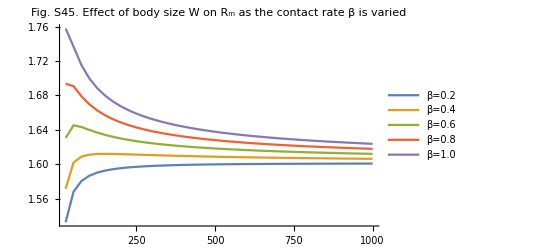
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],RmAcrossWB[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"β=0.2","β=0.4","β=0.6","β=0.8","β=1.0"},PlotLabel->"Fig. S45. Effect of body size W on R_m \nas the contact rate β is varied",PlotRange->All],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

Varying W and γ:

```mathematica
RmAcrossWg=Table[Table[RmSimp/.allom/.allompars/.{βS1->1,βS2->1,βI1->1,βI2->1,βD1->1,βD2->1,σD1->1,σD2->1,σC1->1,σC2->1,γ->g,W->Wval,T->270,f->0.9,a->0.8,x1->1/2,x2->1/2},{Wval,25,1000,25}],{g,0.02,0.1,0.02}];
```

Now, increasing host body size decreases R_m (Fig. S46) across the range of γ values.

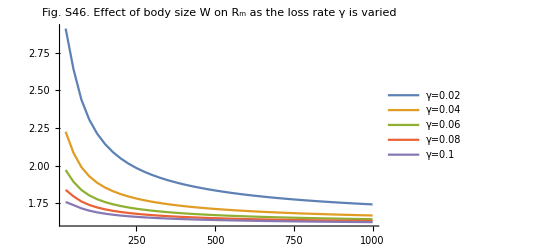
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],RmAcrossWg[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"γ=0.02","γ=0.04","γ=0.06","γ=0.08","γ=0.1"},PlotLabel->"Fig. S46. Effect of body size W on R_m \nas the loss rate γ is varied",PlotRange->All],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

The effect of mass and temperature:

```mathematica
RmAcrossWT=Table[Table[RmSimp/.allom/.allompars/.{βS1->1,βS2->1,βI1->1,βI2->1,βD1->1,βD2->1,σD1->1,σD2->1,σC1->1,σC2->1,γ->0.05,σ2->1,W->Wval,T->Tval,σ1->1,f->0.9,a->0.8,x1->1/2,x2->1/2},{Wval,25,1000,25}],{Tval,270,310,10}];
```

Again, we see a complex relationship between body mass and R_m, but increasing temperature always decreases R_m, regardless of the value of W (Fig. S47).

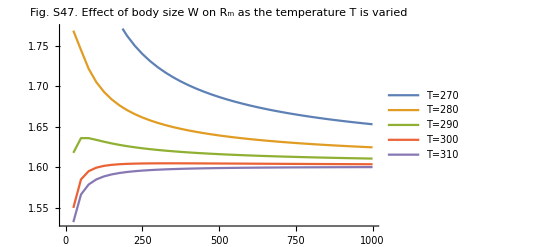
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],RmAcrossWT[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"T=270","T=280","T=290","T=300","T=310"},PlotLabel->"Fig. S47. Effect of body size W on R_m \nas the temperature T is varied"],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

#### Ectoparasites:

Many of the parameters of the model are set by the allometric relationships (Gillooly et al. 2001, Allen et al. 2002, Savage et al. 2004, Poulin & George-Nascimento 2007), and thus can be set to biologically reasonable values.

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(5/12),λ2->λ0 Exp[-Ε/(k T)] (f W)^(5/12),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,Ε->0.43};
```

That leaves a much smaller subset of parameters that can be varied. For simplicity, we focus on parameters whose effects on invasion fitness are indeterminate. This excludes parameters related to the costs associated with generalism, including c (the reduction in shedding rate for generalists), σ_1 (the probability of coinfection, which hold constant at 1), and x_1 (the fraction of host resources captured by the resident strains in coinfection). None of these parameters affect the equilibrium abundances of susceptible and singly infected hosts, so their effect on R_m are predictable and obvious - reducing c, reducing σ_1, or increasing x_1 will all reduce R_m, making invasion more difficult. Thus the only parameters to explore (other than host mass W and temperature T), are β (the contact rate between hosts and parasites, which is assumed to be dependent on the parasite and thus equal for both hosts) and γ (the loss rate of parasites from the environment).

Varying W and β:

```mathematica
RmSimp=Rm2/.I1sEq[[1]]/.I2sEq[[1]]/.D1ssEq[[1]]/.D2ssEq[[1]]/.P1Eq[[2]]/.P2Eq[[2]]/.allom/.allompars;
```

```mathematica
RmAcrossWB=Table[Table[RmSimp/.allom/.allompars/.{βS1->B,βS2->B,βI1->B,βI2->B,βD1->B,βD2->B,σD1->1,σD2->1,σC1->1,σC2->1,γ->0.1,W->Wval,T->270,f->0.9,a->0.8,x1->1/2,x2->1/2},{Wval,25,1000,25}],{B,2,10,2}];
```

Interestingly, here we see a unimodal response of R_m to increasing mass (Fig. S48).

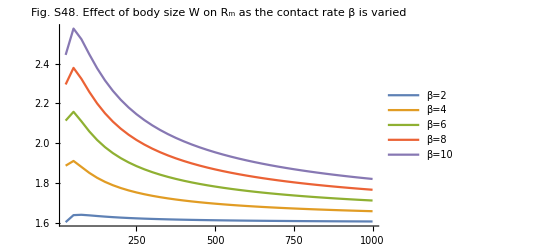
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],RmAcrossWB[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"β=2","β=4","β=6","β=8","β=10"},PlotLabel->"Fig. S48. Effect of body size W on R_m \nas the contact rate β is varied",PlotRange->All],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

Varying W and γ:

```mathematica
RmAcrossWg=Table[Table[RmSimp/.allom/.allompars/.{βS1->5,βS2->5,βI1->5,βI2->5,βD1->5,βD2->5,σD1->1,σD2->1,σC1->1,σC2->1,γ->g,W->Wval,T->270,f->0.9,a->0.8,x1->1/2,x2->1/2},{Wval,25,1000,25}],{g,0.02,0.1,0.02}];
```

We see a similar unimodal response of R_m to increasing host body size (Fig. S49) across the range of γ values.

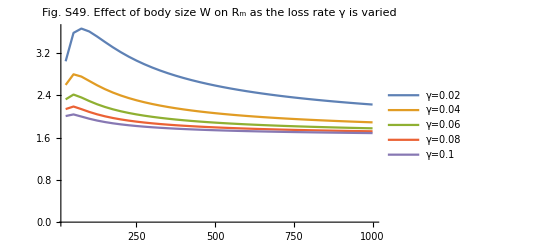
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],RmAcrossWg[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"γ=0.02","γ=0.04","γ=0.06","γ=0.08","γ=0.1"},PlotLabel->"Fig. S49. Effect of body size W on R_m \nas the loss rate γ is varied",PlotRange->All],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

The effect of mass and temperature:

```mathematica
RmAcrossWT=Table[Table[RmSimp/.allom/.allompars/.{βS1->5,βS2->5,βI1->5,βI2->5,βD1->5,βD2->5,σD1->1,σD2->1,σC1->1,σC2->1,γ->0.05,σ2->1,W->Wval,T->Tval,σ1->1,f->0.9,a->0.8,x1->1/2,x2->1/2},{Wval,25,1000,25}],{Tval,270,310,10}];
```

Again, we see a complex relationship between body mass and R_m, but increasing temperature always decreases R_m, regardless of the value of W (Fig. S50).

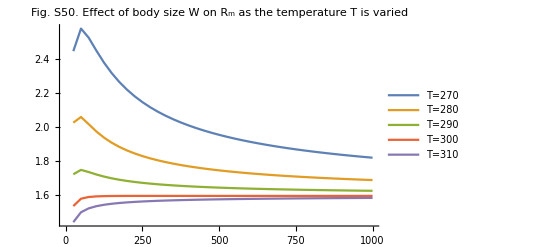
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],RmAcrossWT[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"T=270","T=280","T=290","T=300","T=310"},PlotLabel->"Fig. S50. Effect of body size W on R_m \nas the temperature T is varied"],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

### Case 10: Two specialist parasites; coinfection, constant host population size; no avoidance of non-susceptible hosts

Here we cannot simplify the R_m expression unless we are willing to make some simplifying assumptions. In particular, if we assume that contact rates are host species-specific, but not host class-specific, so β_S_1=β_I_1=β_D_1=β_1 and β_S_2=β_I_2=β_D_2=β_2, then we can get a lot of nice simplification.
 R_m=(β_1(1-OverHat[I_(1,s)]-OverHat[D_(1,s,s)]))/(β_1 K_1+β_2 K_2+γ) (μ_1/(μ_1+σ_C_1 β_1 OverHat[P_1]) (a λ_1 K_1)/μ_1+(σ_C_1 β_1 OverHat[P_1])/(μ_1+σ_C_1 β_1 OverHat[P_1]) (a (1-x_1)λ_1 K_1)/μ_1)+(β_1 OverHat[I_(1,s)])/(β_1 K_1+β_2 K_2+γ)(a (1-x_1)λ_1 K_1)/μ_1+(β_2(1-OverHat[I_(2,s)]-OverHat[D_(2,s,s)]))/(β_2 K_1+β_2 K_2+γ) (μ_2/(μ_2+σ_C_2 β_2 OverHat[P_2]) (a λ_2 K_2)/μ_2+(σ_C_2 β_2 OverHat[P_2])/(μ_2+σ_C_2 β_2 OverHat[P_2]) (a (1-x_2)λ_2 K_2)/μ_2)+(β_2 OverHat[I_(2,s)])/(β_1 K_1+β_2 K_2+γ)(a (1-x_2)λ_2 K_2)/μ_2

```mathematica
Rm2=Rm/.{βS1->β1,βI1->β1,βD1->β1,βS2->β2,βI2->β2,βD2->β2}//Simplify
```

(a (-(I1s K1 (-1+x1) β1 λ1 σC1)/μ1+((-1+D1ss+I1s) K1 β1 λ1 (-μ1+P1 (-1+x1) β1 σC1))/(μ1 (μ1+P1 β1 σC1))-(I2s K2 (-1+x2) β2 λ2 σC2)/μ2+((-1+D2ss+I2s) K2 β2 λ2 (-μ2+P2 (-1+x2) β2 σC2))/(μ2 (μ2+P2 β2 σC2))))/(K1 β1+K2 β2+γ)

In the absence of the generalist parasite, the equilibria are much less complicated than before.

```mathematica
(* Solving for the equilibria of the Subscript[I, 1,s]-Subscript[D, 1,s,s]-Subscript[P, 1] system *)
(* D1ss in terms of Subscript[P, 1] and Subscript[I, 1,s] *)
D1ssEq=Solve[(dI1sdt/.{C1sg->0,Pg->0,I1g->0}/.{βS1->β1,βI1->β1,βD1->β1})==0,D1ss];
(* Subscript[I, 1,s] in terms of Subscript[P, 1] *)
 I1sEq=Solve[(dD1ssdt/.D1ssEq[[1]]/.{βS1->β1,βI1->β1,βD1->β1})==0,I1s];
(* Subscript[D, 1,s,s] in terms of Subscript[P, 1] *)
D1ssEq=Simplify[D1ssEq/.I1sEq[[1]]];
(* Subscript[P, 1] equilibrium *)
P1Eq=Solve[(dP1dt/.{C1sg->0,Pg->0,I1g->0}/.{βS1->β1,βI1->β1,βD1->β1}/.I1sEq[[1]]/.D1ssEq[[1]])==0,P1]//Simplify
(* Subscript[D, 1,s,s] equilibrium *)
D1ssEq=Simplify[D1ssEq/.P1Eq[[2]]]
(* Subscript[I, 1,s] equilibrium *)
I1sEq=Simplify[I1sEq/.P1Eq[[2]]]
(* Solving for the equilibria of the Subscript[I, 2,s]-Subscript[D, 2,s,s]-Subscript[P, 2] system *)
(* D2ss in terms of Subscript[P, 2] and Subscript[I, 2,s] *)
D2ssEq=Solve[(dI2sdt/.{C2sg->0,Pg->0,I2g->0}/.{βS2->β2,βI2->β2,βD2->β2})==0,D2ss];
(* Subscript[I, 2,s] in terms of Subscript[P, 2] *)
 I2sEq=Solve[(dD2ssdt/.D2ssEq[[1]]/.{βS2->β2,βI2->β2,βD2->β2})==0,I2s];
(* Subscript[D, 2,s,s] in terms of Subscript[P, 2] *)
D2ssEq=Simplify[D2ssEq/.I2sEq[[1]]/.{βS2->β2,βI2->β2,βD2->β2}];
(* Subscript[P, 2] equilibrium *)
P2Eq=Solve[(dP2dt/.{C2sg->0,Pg->0,I2g->0}/.{βS2->β2,βI2->β2,βD2->β2}/.I2sEq[[1]]/.D2ssEq[[1]])==0,P2]//Simplify
(* Subscript[D, 2,s,s] equilibrium *)
D2ssEq=Simplify[D2ssEq/.P2Eq[[2]]]
(* Subscript[I, 2,s] equilibrium *)
I2sEq=Simplify[I2sEq/.P2Eq[[2]]]
```

{{P1→0},{P1→(K1 β1 (λ1-μ1)-γ μ1)/(β1 (K1 β1+γ))}}

{{D1ss→((K1 β1 (λ1-μ1)-γ μ1)^2 σD1)/(K1 β1 λ1 (-γ μ1 (-1+σD1)+K1 β1 (μ1+λ1 σD1-μ1 σD1)))}}

{{I1s→-(((K1 β1+γ) μ1 (γ μ1+K1 β1 (-λ1+μ1)))/(K1 β1 λ1 (-γ μ1 (-1+σD1)+K1 β1 (μ1+λ1 σD1-μ1 σD1))))}}

{{P2→0},{P2→(K2 β2 (λ2-μ2)-γ μ2)/(β2 (K2 β2+γ))}}

{{D2ss→((K2 β2 (λ2-μ2)-γ μ2)^2 σD2)/(K2 β2 λ2 (-γ μ2 (-1+σD2)+K2 β2 (μ2+λ2 σD2-μ2 σD2)))}}

{{I2s→-(((K2 β2+γ) μ2 (γ μ2+K2 β2 (-λ2+μ2)))/(K2 β2 λ2 (-γ μ2 (-1+σD2)+K2 β2 (μ2+λ2 σD2-μ2 σD2))))}}

We can plug these equilibria into the expression and are again stuck unless we are willing to make some simplifying assumptions.

```mathematica
Simplify[Rm2/.P1Eq[[2]]/.D1ssEq[[1]]/.I1sEq[[1]]/.P2Eq[[2]]/.D2ssEq[[1]]/.I2sEq[[1]]]
```

1/(K1 β1+K2 β2+γ)a (-(((K1 β1+γ) (γ μ1 (1+(-1+x1) σC1)+K1 β1 (μ1+λ1 σC1-x1 λ1 σC1-μ1 σC1+x1 μ1 σC1)))/(γ μ1 (-1+σC1)+K1 β1 (μ1 (-1+σC1)-λ1 σC1)))-((K2 β2+γ) (γ μ2 (1+(-1+x2) σC2)+K2 β2 (μ2+λ2 σC2-x2 λ2 σC2-μ2 σC2+x2 μ2 σC2)))/(γ μ2 (-1+σC2)+K2 β2 (μ2 (-1+σC2)-λ2 σC2))+((-1+x1) (K1 β1+γ) (γ μ1+K1 β1 (-λ1+μ1)) σC1)/(-γ μ1 (-1+σD1)+K1 β1 (μ1+λ1 σD1-μ1 σD1))+((-1+x2) (K2 β2+γ) (γ μ2+K2 β2 (-λ2+μ2)) σC2)/(-γ μ2 (-1+σD2)+K2 β2 (μ2+λ2 σD2-μ2 σD2)))

In particular, we assume that σ_C_1=σ_D_1=σ_C_2=σ_D_2=1 and that host resources are partitioned equally between coinfecting strains (x_1=x_2=0.5), then the R_m expression simplifies considerably, to R_m=a(1+(2 γ)/(β_1 K_1+β_2 K_2+γ)).

This is the same expression as we encountered in Case 6 above. From this expression, it is immediately clear how changing body sizes or temperature will affect R_m, because R_m depends only on the abundances of each host. Since increasing body size reduces abundance, (∂R_m)/(∂W)>0. Since increasing temperature decreases abundance, (∂R_m)/(∂W)>0. This will be true for both endoparasites and ectoparasites.

```mathematica
Simplify[Rm2/.P1Eq[[2]]/.D1ssEq[[1]]/.I1sEq[[1]]/.P2Eq[[2]]/.D2ssEq[[1]]/.I2sEq[[1]]/.{σD2->1,σD1->1,σC1->1,σC2->1,x1->1/2,x2->1/2}]
```

(a (K1 β1+K2 β2+2 γ))/(K1 β1+K2 β2+γ)

Appendix B: Deriving the invasion condition and analysis of models in Table 3

## Appendix B: Trophically transmitted parasites

### Case 1: One specialist parasite; avoidance of infected intermediate hosts

Let D_1 and D_2 be two definitive hosts and N be prey of both and the intermediate host. One touchy bit is how to deal with the effect of ingestion on both the dynamics of predator (the definitive host) and prey (the intermediate host). One possibility is that infection is embedded within a classic predator-prey model, where both predator and prey growth are impacted by one another. Such a model is quite different from the direct life cycle model studied in the main text, and is also very difficult to analyze. A second possibility is that prey density is constant; in this model you cannot assume that predator growth is entirely determined by prey ingestion (as in a classic predator-prey model) because the predator population will either grow or decay exponentially. 

Here we assume that the intermediate host (the prey) has a constant population size. We let N_T be the total population size, and N_(I,r) and N_(I,m) be the abundance of intermedate host infected with the resident (specialist) and mutant (generalist) parasites, respectively. We don’t need to track the number of susceptible intermediate hosts. The two definitive hosts both grow logistically in the absence of infection, with no direct effect of prey ingestion on their growth rate. One way to justify this assumption is to assume that the predators are eating lots of different prey items, so that their dynamics are largely independent of this particular prey item. However, infection is assumed to have an effect on the growth of the definitive host. We let D_(1,S) and D_(2,S) to be the number of primary and secondary definitive hosts that are susceptible to infection; D_(1,I,r) is the number of primary definitive hosts infected by the specialist (resident) parasite; we assume that the secondary definitive host is not infected by its own specialist parasite. D_(1,I,m) and D_(2,I,m) are the numbers of primary and secondary definitive hosts infected by the generalist (mutant) parasite. Definitive hosts shed parasite back into the environment, with P_r and P_m the abundance of specialist and generalist in the environment. These parasites are consumed by the intermediate host, which can then transmit the parasite to the definitive host upon ingestion.

Note that there is no need to consider active vs. passive host seeking here, as there is only a single intermediate host that is assumed to contact parasites in the environment. 

The full system is given below.

```mathematica
dNirdt=β (NT-Nir-Nim) Pr-a1 (D1s+D1ir+D1im)Nir-a2(D2s+D2im) Nir;
dNimdt=β (NT-Nir-Nim) Pm-a1 (D1s+D1ir+D1im)Nim-a2 (D2s+D2im) Nim;
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim);
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;
dPrdt=λ1 D1ir-β (NT-Nir-Nim) Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β (NT-Nir-Nim) Pm-γ Pm;
```

The Jacobian matrix for this system is quite large, but has the same block triangular structure that we have observed previously.

```mathematica
(* The Jacobian matrix of partial derivatives *)
J={{D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
(* The Jacobian, evaluated at the equilibrium where the generalist is absent *)
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 Nir+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
-a1 Nir | -a2 Nir | -a1 (D1ir+D1s)-a2 D2s-Pr β | -a1 Nir | (-Nir+NT) β | -Pr β | -a1 Nir | -a2 Nir | 0
a1 Nir | 0 | a1 D1s | -μ1 | 0 | 0 | 0 | 0 | 0
0 | 0 | Pr β | λ1 | -(-Nir+NT) β-γ | Pr β | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s)-a2 D2s | 0 | 0 | (-Nir+NT) β
0 | 0 | 0 | 0 | 0 | a1 D1s | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | a2 D2s | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -(-Nir+NT) β-γ)

Because J is upper block triangular, the eigenvalues are given by the eigenvalues of the submatrices that fall on the diagonal of J. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below.

```mathematica
MatrixForm[J[[6;;9,6;;9]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s)-a2 D2s | 0 | 0 | (-Nir+NT) β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -(-Nir+NT) β-γ)

We can apply the next generation matrix theorem to determine the stability by rewriting J=F-V and looking at the spectral radius of F.V^-1.

```mathematica
(* Define the F and V matrices *)
F={{0,0,0, β (NT-Nir)},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 (D1ir+D1s)+a2 D2s,0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β (NT-Nir)+γ}};
(* Confirming that J=F-V *)
(J[[6;;9,6;;9]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
(* Calculating the spectral radius *)
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,(c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),-(((-1)^(1/3) c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3))),((-1)^(2/3) c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue, which can be rewritten as R_m=(β N_s N_T)/(β N_s N_T+γ)((a_1 D_(1,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S))(c λ_1)/μ_1+(a_2 D_(2,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S))(c λ_2)/μ_2), which has a nice intuitive meaning: (β (N_T-N_(I r)))/(β (N_T-N_(I r))+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; (a_1 D_(1,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S)) is the probability that an infected intermediate host is ingested by a susceptible primary definitive host; (a_2 D_(2,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S)) is the probability that an infected intermediate host is ingested by a suceptible secondary definitive host; (c λ_1)/μ_1 and (c λ_2)/μ_2 are the expected number of parasites shed from infected primary and secondary definitive hosts, respectively.

```mathematica
(* Confirming the biologically meaningful form of Subscript[R, m] *)
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β (NT-Nir))/(β (NT-Nir)+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)//Simplify
```

True

To determine how changing parameters affects R_0 for this model, we need to know the equilibrium values of N_s, D_(1,S), D_(1,I,r), and D_(2,S) when the generalist parasite is not present. We know that D_(2,S)=K_2, the carrying capacity for the secondary host, but the other equilibria are too complex to allow for simple analysis. Instead, we will use numerical exploration to see whether changing mass/temperature have any effect on invasion fitness. As before, we use simple allometric scaling relationships to relate key processes to host body size and temperature. Additionally, we assume that the growth rate of the definitive host (r) depends on body size as well.
r=r_0 e^(E/k T)W^-0.25
K=K_0 e^(E/k T)W^-0.75
μ = μ_0 e^(-E/k T)W^-0.25
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites).

Values for .08.08E, k, r_0,K_0, and μ_0 that are appropriate for fish come from Savage et al. 2004. The estimate of λ_0 is modified from Poulin & George-Nascimento 2007. 

The function below uses numerical simulation to determine the equilibrium values of N_s, D_(1,S), D_(1,I,r), and D_(2,S) for the specified parameters. These values are then plugged into the R_m expression to calculate the invasion fitness.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
Nir'[t]==β (NT-Nir[t]) Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t],
D1ir'[t]==a1 D1s[t] Nir[t]-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β (NT-Nir[t]) Pr[t]-γ Pr[t],
Nir[0]==0,
D1s[0]==0.1,
D1ir[0]==0,
Pr[0]==1}/.allom/.pars),
{Ns,Nir,D1s,D1ir,Pr},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{Ns->(Ns[1000]/.Soln)[[1]],Nir->(Nir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],Pr->(Pr[1000]/.Soln)[[1]]}];*)
(β (NT-Nir))/(β (NT-Nir)+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)/.{Nir->(Nir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]]}/.D2s->K2/.allom/.pars
];
```

For these parameters, increasing body size increases R_0:

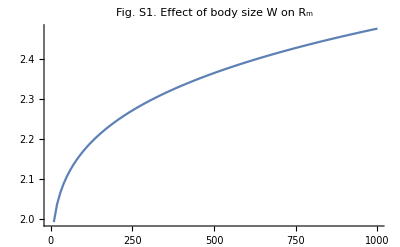
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[{Table[W,{W,10,1000,10}][[i]],InvFitAcrossW[[i]]},{i,1,Length[InvFitAcrossW]}],PlotLabel->"Fig. S1. Effect of body size W on R_m"],{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

This is true if you increase the temperature (here increasing temperature from 270 to 310, Fig. S2). Notice, however, that R_m is lower for higher temperatures, indicating that increasing temperature negatively affects R_0.

```mathematica
InvFitAcrossWT=Table[Table[NumSolInvFit[W,T,0.9,0.9,1,0.1,0.01,0.1],{W,25,1000,25}],{T,270,310,10}];
```

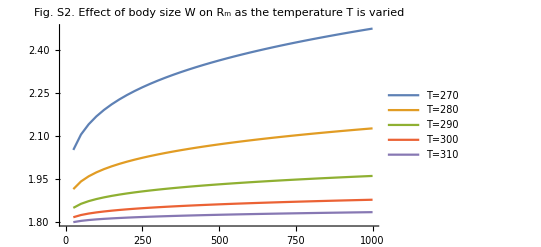
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],InvFitAcrossWT[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"T=270","T=280","T=290","T=300","T=310"},PlotLabel->"Fig. S2. Effect of body size W on R_m \nas the temperature T is varied"],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

It also holds if you increase the cost of generalism (here decreasing c from 0.9 to 0.5; Fig. S3):

```mathematica
InvFitAcrossWc=Table[Table[NumSolInvFit[W,270,c,0.9,1,0.1,0.01,0.1],{W,25,1000,25}],{c,0.5,0.9,0.1}];
```

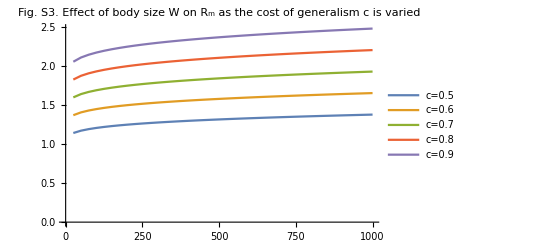
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],InvFitAcrossWc[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"c=0.5","c=0.6","c=0.7","c=0.8","c=0.9"},PlotLabel->"Fig. S3. Effect of body size W on R_m \nas the cost of generalism c is varied"],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

It also holds if you reduce the size of the secondary host (here decreasing f from 0.9 to 0.5; Fig. S4):

```mathematica
InvFitAcrossWf=Table[Table[NumSolInvFit[W,270,0.9,f,1,0.1,0.01,0.1],{W,25,1000,25}],{f,0.5,0.9,0.1}];
```

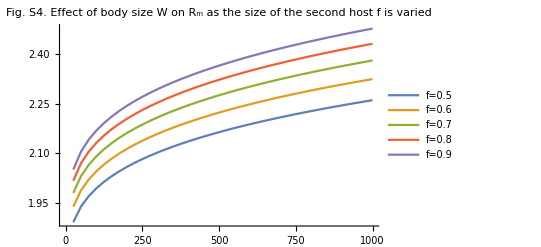
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],InvFitAcrossWf[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"f=0.5","f=0.6","f=0.7","f=0.8","f=0.9"},PlotLabel->"Fig. S4. Effect of body size W on R_m \nas the size of the second host f is varied"],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

It also holds if you reduce the number of intermediate hosts (here N_T ranges from 0.25 to 2; Fig. S5):

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.1,0.01,0.1],{W,25,1000,25}],{NT,0.5,2,0.5}];
```

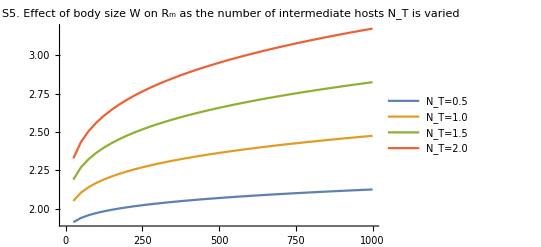
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],InvFitAcrossWNT[[j,i]]},{i,1,40}],{j,1,4}],PlotLegends->{"N_T=0.5","N_T=1.0","N_T=1.5","N_T=2.0"},PlotLabel->"Fig. S5. Effect of body size W on R_m \nas the number of intermediate hosts N_T is varied"],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

It also holds if you change the transmission rate to intermediate hosts (here β ranges from 0.05 to 0.55; Fig. S6):

```mathematica
InvFitAcrossWB=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,B,0.01,0.1],{W,25,1000,25}],{B,0.05,0.55,0.1}];
```

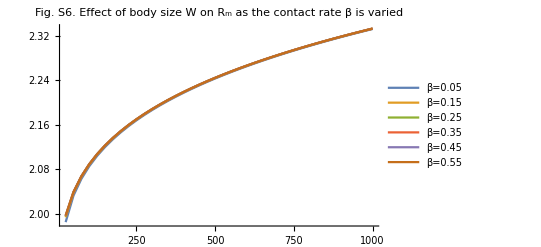
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],InvFitAcrossWB[[j,i]]},{i,1,40}],{j,1,6}],PlotLegends->{"β=0.05","β=0.15","β=0.25","β=0.35","β=0.45","β=0.55"},PlotLabel->"Fig. S6. Effect of body size W on R_m \nas the contact rate β is varied",PlotRange->All],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

It also holds if you change the rate parasites are lost from the environment (here γ ranges from 0.01 to 0.1; Fig. S7):

```mathematica
InvFitAcrossWg=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,g,0.1],{W,25,1000,25}],{g,0.02,0.1,0.02}];
```

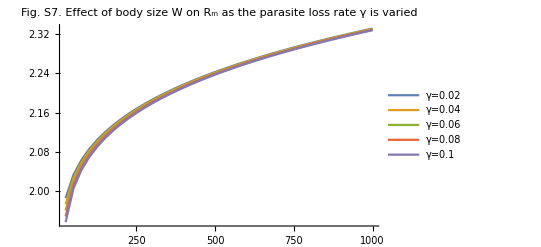
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],InvFitAcrossWg[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"γ=0.02","γ=0.04","γ=0.06","γ=0.08","γ=0.1"},PlotLabel->"Fig. S7. Effect of body size W on R_m \nas the parasite loss rate γ is varied",PlotRange->All],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

It also holds if you change the ingestion rate of the definitive hosts:

```mathematica
InvFitAcrossWa=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,0.01,a],{W,25,1000,25}],{a,0.1,0.5,0.1}];
```

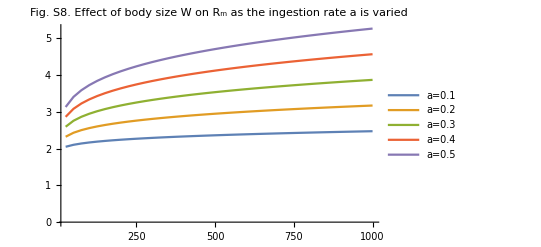
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],InvFitAcrossWa[[j,i]]},{i,1,40}],{j,1,5}],PlotLegends->{"a=0.1","a=0.2","a=0.3","a=0.4","a=0.5"},PlotLabel->"Fig. S8. Effect of body size W on R_m \nas the ingestion rate a is varied",PlotRange->All],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

### Case 2: Two specialist parasites; avoidance of infected intermediate hosts

Now we assume that there are two specialist parasites exploiting the same intermediate host, but infecting different definitive hosts. We let N_(2I r) track the number of intermediate hosts infected with the second specialist parasite and D_(2I r) track the number of secondary definitive hosts infected by the second specialist parasite.

```mathematica
dN1irdt=β (NT-N1ir-N2ir-Nim) P1r-a1(D1s+D1ir+D1im) N1ir-a2(D2s+D2ir+D2im) N1ir;
dN2irdt=β (NT-N1ir-N2ir-Nim) P2r-a1(D1s+D1ir+D1im)N2ir-a2 (D2s+D2ir+D2im) N2ir;
dNimdt=β (NT-N1ir-N2ir-Nim) Pm-a1(D1s+D1ir+D1im) Nim-a2 (D2s+D2ir+D2im) Nim;

dD1sdt=r1 (D1s+D1ir+D1im)(1-(D1s+D1ir+D1im)/K1)-a1 D1s (N1ir+Nim);
dD2sdt=r2 (D2s+D2ir+D2im)(1-(D2s+D2ir+D2im)/K2)-a2 D2s (N2ir+Nim);
dD1irdt=a1 D1s N1ir-μ1 D1ir;
dD2irdt=a2 D2s N2ir-μ2 D2ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;

dP1rdt=λ1 D1ir-β (NT-N1ir-N2ir-Nim) P1r-γ P1r;
dP2rdt=λ2 D2ir-β (NT-N1ir-N2ir-Nim) P2r-γ P2r;
dPmdt=c λ1 D1im+c λ2 D2im-β (NT-N1ir-N2ir-Nim) Pm-γ Pm;
```

To determine whether the generalist can invade this system, we again look at the Jacobian.

```mathematica
J={{D[dN1irdt,N1ir],D[dN1irdt,D1s],D[dN1irdt,D1ir],D[dN1irdt,P1r],
D[dN1irdt,N2ir],D[dN1irdt,D2s],D[dN1irdt,D2ir],D[dN1irdt,P2r],
D[dN1irdt,Nim],D[dN1irdt,D1im],D[dN1irdt,D2im],D[dN1irdt,Pm]},
{D[dD1sdt,N1ir],D[dD1sdt,D1s],D[dD1sdt,D1ir],D[dD1sdt,P1r],
D[dD1sdt,N2ir],D[dD1sdt,D2s],D[dD1sdt,D2ir],D[dD1sdt,P2r],
D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD1irdt,N1ir],D[dD1irdt,D1s],D[dD1irdt,D1ir],D[dD1irdt,P1r],
D[dD1irdt,N2ir],D[dD1irdt,D2s],D[dD1irdt,D2ir],D[dD1irdt,P2r],
D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dP1rdt,N1ir],D[dP1rdt,D1s],D[dP1rdt,D1ir],D[dP1rdt,P1r],
D[dP1rdt,N2ir],D[dP1rdt,D2s],D[dP1rdt,D2ir],D[dP1rdt,P2r],
D[dP1rdt,Nim],D[dP1rdt,D1im],D[dP1rdt,D2im],D[dP1rdt,Pm]},
{D[dN2irdt,N1ir],D[dN2irdt,D1s],D[dN2irdt,D1ir],D[dN2irdt,P1r],
D[dN2irdt,N2ir],D[dN2irdt,D2s],D[dN2irdt,D2ir],D[dN2irdt,P2r],
D[dN2irdt,Nim],D[dN2irdt,D1im],D[dN2irdt,D2im],D[dN2irdt,Pm]},
{D[dD2sdt,N1ir],D[dD2sdt,D1s],D[dD2sdt,D1ir],D[dD2sdt,P1r],
D[dD2sdt,N2ir],D[dD2sdt,D2s],D[dD2sdt,D2ir],D[dD2sdt,P2r],
D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dD2irdt,N1ir],D[dD2irdt,D1s],D[dD2irdt,D1ir],D[dD2irdt,P1r],
D[dD2irdt,N2ir],D[dD2irdt,D2s],D[dD2irdt,D2ir],D[dD2irdt,P2r],
D[dD2irdt,Nim],D[dD2irdt,D1im],D[dD2irdt,D2im],D[dD2irdt,Pm]},
{D[dP2rdt,N1ir],D[dP2rdt,D1s],D[dP2rdt,D1ir],D[dP2rdt,P1r],
D[dP2rdt,N2ir],D[dP2rdt,D2s],D[dP2rdt,D2ir],D[dP2rdt,P2r],
D[dP2rdt,Nim],D[dP2rdt,D1im],D[dP2rdt,D2im],D[dP2rdt,Pm]},
{D[dNimdt,N1ir],D[dNimdt,D1s],D[dNimdt,D1ir],D[dNimdt,P1r],
D[dNimdt,N2ir],D[dNimdt,D2s],D[dNimdt,D2ir],D[dNimdt,P2r],
D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,N1ir],D[dD1imdt,D1s],D[dD1imdt,D1ir],D[dD1imdt,P1r],
D[dD1imdt,N2ir],D[dD1imdt,D2s],D[dD1imdt,D2ir],D[dD1imdt,P2r],
D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,N1ir],D[dD2imdt,D1s],D[dD2imdt,D1ir],D[dD2imdt,P1r],
D[dD2imdt,N2ir],D[dD2imdt,D2s],D[dD2imdt,D2ir],D[dD2imdt,P2r],
D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,N1ir],D[dPmdt,D1s],D[dPmdt,D1ir],D[dPmdt,P1r],
D[dPmdt,N2ir],D[dPmdt,D2s],D[dPmdt,D2ir],D[dPmdt,P2r],
D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}}/.{Nim->0,D1im->0,D2im->0,Pm->0};
```

As before, this matrix is upper block triangular. The upper left submatrix determines the stability of the system that doesn’t include the generalist parasite. Whether the generalist can invade the system depends on the eigenvalues of the lower right submatrix of J:

```mathematica
MatrixForm[J[[9;;12,9;;12]]]
```

(-a1 (D1ir+D1s)-a2 (D2ir+D2s) | 0 | 0 | (-N1ir-N2ir+NT) β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -(-N1ir-N2ir+NT) β-γ)

Using the next generation matrix theorem, the Jacobian will have a positive eigenvalue whenever the spectral radius, given by the second value below, is greater than 1.

```mathematica
(* Define F and V *)
F={{0,0,0,(NT-N1ir-N2ir) β},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1,c λ2,0}};
V={{a1 (D1ir+D1s)+a2(D2ir+D2s),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,(NT-N1ir-N2ir) β+γ}};
(* Confirming that J=F-V *)
J[[9;;12,9;;12]]==F-V//Simplify
(* Stability is determined by the spectral radius of F.V^-1*)
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,(c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),-(((-1)^(1/3) c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3))),((-1)^(2/3) c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3))}

The spectral radius is equivalent to R_m=(β N_s N_T)/(β N_s N_T+γ)((a_1 D_(1,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S))(c λ_1)/μ_1+(a_2 D_(2,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S))(c λ_2)/μ_2).

```mathematica
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==((NT-N1ir-N2ir) β)/((NT-N1ir-N2ir) β+γ) (((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s))) (c λ1)/μ1+((a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s))) (c λ2)/μ2)//Simplify
```

True

However, as before, it is impossible to make headway analytically, so we must resort to numerical solutions. The code below simulates the ODE system and computes the value of R_m.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};
(*Print[(β NT)/(β NT+γ)((a1 K1)/(a1 K1+a2 K2) λ1/μ1)/.allom/.pars];*)
(*Print[(β NT)/(β NT+γ)((a2 K2)/(a1 K1+a2 K2) λ2/μ2)/.allom/.pars];*)
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
N1ir'[t]==β (NT-N1ir[t]-N2ir[t]) P1r[t]-a1(D1s[t]+D1ir[t]) N1ir[t]-a2(D2s[t]+D2ir[t]) N1ir[t],
N2ir'[t]==β (NT-N1ir[t]-N2ir[t]) P2r[t]-a1(D1s[t]+D1ir[t]) N2ir[t]-a2(D2s[t]+D2ir[t]) N2ir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] N1ir[t],
D2s'[t]==r2 (D2s[t]+D2ir[t]) (1-(D2s[t]+D2ir[t])/K2)-a2 D2s[t] N2ir[t],
D1ir'[t]==a1 D1s[t] N1ir[t]-μ1 D1ir[t],
D2ir'[t]==a2 D2s[t] N2ir[t]-μ1 D2ir[t],
P1r'[t]==λ1 D1ir[t]-β (NT-N1ir[t]-N2ir[t]) P1r[t]-γ P1r[t],
P2r'[t]==λ1 D1ir[t]-β (NT-N1ir[t]-N2ir[t]) P2r[t]-γ P2r[t],
N1ir[0]==0,N2ir[0]==0,
D1s[0]==0.1,D2s[0]==0.1,
D1ir[0]==0,D2ir[0]==0,
P1r[0]==1,P2r[0]==1}/.allom/.pars),
{N1ir,N2ir,D1s,D1ir,D2s,D2ir,P1r,P2r},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}] *);
((NT-N1ir-N2ir) β)/((NT-N1ir-N2ir) β+γ) (((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s))) (c λ1)/μ1+((a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s))) (c λ2)/μ2)/.{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}/.allom/.pars
];
```

One case is sufficient to demonstrate that the response of the generalist’s R_m to changes in host body size is much more complex here. Consider the effect of changing the definitive host body sizes across a gradient of intermediate host abundance. You can see very clearly that the responses depend on the value of N_T: when N_T is small, increasing host mass increases R_m; when N_T is large, increasing host mass first increases, then decreases R_m (Fig. S9).

In reality, the abundance of the definitive host’s prey is likely to be related to the size of the definitive host: in general, larger-bodied hosts are more likely to consume larger-bodied prey, whose carrying capacities would decrease commensurately. That is, as definitive host body size goes up, you would expect intermediate host carrying capacity to go down.

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.01,0.1,0.01],{W,25,1000,25}],{NT,{0.1,0.2,0.5,1,1.5,2}}];
```

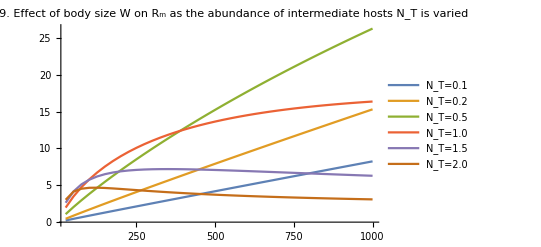
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],InvFitAcrossWNT[[j,i]]},{i,1,40}],{j,1,6}],PlotLegends->{"N_T=0.1","N_T=0.2","N_T=0.5","N_T=1.0","N_T=1.5","N_T=2.0"},PlotLabel->"Fig. S9. Effect of body size W on R_m \nas the abundance of intermediate hosts N_T is varied",PlotRange->All],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

Increasing temperature also has a much more complex effect on R_m: when N_T is large, increasing temperature increases R_m (Fig. S10), but when N_T is small, increasing temperature decreases R_m (Fig. S11).

```mathematica
(* Variation in Subscript[R, m] as T varies when Subscript[N, T]=2 *)
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,2,0.01,0.1,0.01],{T,270,310,2}];
```

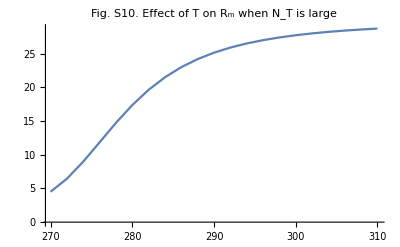
-Graphics-Temperature TGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[{Table[T,{T,270,310,2}][[i]],InvFitAcrossWT[[i]]},{i,1,21}],PlotLabel->"Fig. S10. Effect of T on R_m when N_T is large"],
{"Temperature T","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

```mathematica
(* Variation in Subscript[R, m] as T varies when Subscript[N, T]=0.1 *)
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,0.1,0.01,0.1,0.01],{T,270,310,2}];
```

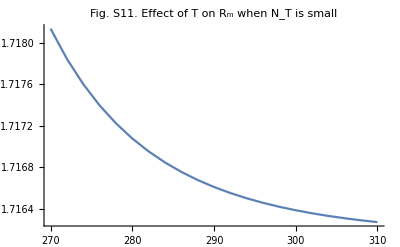
-Graphics-Temperature TGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[{Table[T,{T,270,310,2}][[i]],InvFitAcrossWT[[i]]},{i,1,21}],PlotLabel->"Fig. S11. Effect of T on R_m when N_T is small"],
{"Temperature T","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

### Case 3: Two specialist parasites; no avoidance of infected intermediate hosts

This case assumes that the parasite cannot determine whether an intermediate host is infected or not. Thus both susceptible and infected intermediate hosts remove parasites from the environment, but only consumption by a susceptible host can produce a new infection.

```mathematica
dN1irdt=β (NT-N1ir-N2ir-Nim) P1r-a1(D1s+D1ir+D1im) N1ir-a2(D2s+D2ir+D2im) N1ir;
dN2irdt=β (NT-N1ir-N2ir-Nim) P2r-a1(D1s+D1ir+D1im)N2ir-a2 (D2s+D2ir+D2im) N2ir;
dNimdt=β (NT-N1ir-N2ir-Nim) Pm-a1(D1s+D1ir+D1im) Nim-a2 (D2s+D2ir+D2im) Nim;

dD1sdt=r1 (D1s+D1ir+D1im)(1-(D1s+D1ir+D1im)/K1)-a1 D1s (N1ir+Nim);
dD2sdt=r2 (D2s+D2ir+D2im)(1-(D2s+D2ir+D2im)/K2)-a2 D2s (N2ir+Nim);
dD1irdt=a1 D1s N1ir-μ1 D1ir;
dD2irdt=a2 D2s N2ir-μ2 D2ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;

dP1rdt=λ1 D1ir-β NT P1r-γ P1r;
dP2rdt=λ2 D2ir-β NT P2r-γ P2r;
dPmdt=c λ1 D1im+c λ2 D2im-β NT Pm-γ Pm;
```

To determine whether the generalist can invade this system, we again look at the Jacobian.

```mathematica
J={{D[dN1irdt,N1ir],D[dN1irdt,D1s],D[dN1irdt,D1ir],D[dN1irdt,P1r],
D[dN1irdt,N2ir],D[dN1irdt,D2s],D[dN1irdt,D2ir],D[dN1irdt,P2r],
D[dN1irdt,Nim],D[dN1irdt,D1im],D[dN1irdt,D2im],D[dN1irdt,Pm]},
{D[dD1sdt,N1ir],D[dD1sdt,D1s],D[dD1sdt,D1ir],D[dD1sdt,P1r],
D[dD1sdt,N2ir],D[dD1sdt,D2s],D[dD1sdt,D2ir],D[dD1sdt,P2r],
D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD1irdt,N1ir],D[dD1irdt,D1s],D[dD1irdt,D1ir],D[dD1irdt,P1r],
D[dD1irdt,N2ir],D[dD1irdt,D2s],D[dD1irdt,D2ir],D[dD1irdt,P2r],
D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dP1rdt,N1ir],D[dP1rdt,D1s],D[dP1rdt,D1ir],D[dP1rdt,P1r],
D[dP1rdt,N2ir],D[dP1rdt,D2s],D[dP1rdt,D2ir],D[dP1rdt,P2r],
D[dP1rdt,Nim],D[dP1rdt,D1im],D[dP1rdt,D2im],D[dP1rdt,Pm]},
{D[dN2irdt,N1ir],D[dN2irdt,D1s],D[dN2irdt,D1ir],D[dN2irdt,P1r],
D[dN2irdt,N2ir],D[dN2irdt,D2s],D[dN2irdt,D2ir],D[dN2irdt,P2r],
D[dN2irdt,Nim],D[dN2irdt,D1im],D[dN2irdt,D2im],D[dN2irdt,Pm]},
{D[dD2sdt,N1ir],D[dD2sdt,D1s],D[dD2sdt,D1ir],D[dD2sdt,P1r],
D[dD2sdt,N2ir],D[dD2sdt,D2s],D[dD2sdt,D2ir],D[dD2sdt,P2r],
D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dD2irdt,N1ir],D[dD2irdt,D1s],D[dD2irdt,D1ir],D[dD2irdt,P1r],
D[dD2irdt,N2ir],D[dD2irdt,D2s],D[dD2irdt,D2ir],D[dD2irdt,P2r],
D[dD2irdt,Nim],D[dD2irdt,D1im],D[dD2irdt,D2im],D[dD2irdt,Pm]},
{D[dP2rdt,N1ir],D[dP2rdt,D1s],D[dP2rdt,D1ir],D[dP2rdt,P1r],
D[dP2rdt,N2ir],D[dP2rdt,D2s],D[dP2rdt,D2ir],D[dP2rdt,P2r],
D[dP2rdt,Nim],D[dP2rdt,D1im],D[dP2rdt,D2im],D[dP2rdt,Pm]},
{D[dNimdt,N1ir],D[dNimdt,D1s],D[dNimdt,D1ir],D[dNimdt,P1r],
D[dNimdt,N2ir],D[dNimdt,D2s],D[dNimdt,D2ir],D[dNimdt,P2r],
D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,N1ir],D[dD1imdt,D1s],D[dD1imdt,D1ir],D[dD1imdt,P1r],
D[dD1imdt,N2ir],D[dD1imdt,D2s],D[dD1imdt,D2ir],D[dD1imdt,P2r],
D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,N1ir],D[dD2imdt,D1s],D[dD2imdt,D1ir],D[dD2imdt,P1r],
D[dD2imdt,N2ir],D[dD2imdt,D2s],D[dD2imdt,D2ir],D[dD2imdt,P2r],
D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,N1ir],D[dPmdt,D1s],D[dPmdt,D1ir],D[dPmdt,P1r],
D[dPmdt,N2ir],D[dPmdt,D2s],D[dPmdt,D2ir],D[dPmdt,P2r],
D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}}/.{Nim->0,D1im->0,D2im->0,Pm->0};
```

As before, this matrix is upper block triangular. The upper left submatrix determines the stability of the system that doesn’t include the generalist parasite. Whether the generalist can invade the system depends on the eigenvalues of the lower right submatrix of J:

```mathematica
MatrixForm[J[[9;;12,9;;12]]]
```

(-a1 (D1ir+D1s)-a2 (D2ir+D2s) | 0 | 0 | (-N1ir-N2ir+NT) β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -NT β-γ)

Using the next generation matrix theorem, the invasion of the generalist requires that one of the following eigenvalues be larger than 1 in magnitude.

```mathematica
(* Defining F and V *)
F={{0,0,0,(NT-N1ir-N2ir) β},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1,c λ2,0}};
V={{a1 (D1ir+D1s)+a2(D2ir+D2s),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β NT+γ}};
(* Confirming that J = F-V *)
J[[9;;12,9;;12]]==F-V//Simplify
(* Calculating the spectral radius of F.V^-1 *)]
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(c (NT-N1ir-N2ir) β (a2 D2s λ2 μ1+a1 D1s λ1 μ2))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s) (NT β+γ) μ1 μ2)//Simplify
```

The invasion condition can be rewritten as:

```mathematica
(c (NT-N1ir-N2ir) β (a2 D2s λ2 μ1+a1 D1s λ1 μ2))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s) (NT β+γ) μ1 μ2)==(β (NT-N1ir-N2ir))/(β NT+γ)(((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s))) (c λ1)/μ1+((a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s))) (c λ2)/μ2)//Simplify
```

True

As before, it is impossible to make headway analytically, so we must resort to numerical solutions.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};
(*Print[(β NT)/(β NT+γ)((a1 K1)/(a1 K1+a2 K2) λ1/μ1)/.allom/.pars];*)
(*Print[(β NT)/(β NT+γ)((a2 K2)/(a1 K1+a2 K2) λ2/μ2)/.allom/.pars];*)
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
N1ir'[t]==β (NT-N1ir[t]-N2ir[t]) P1r[t]-a1(D1s[t]+D1ir[t]) N1ir[t]-a2(D2s[t]+D2ir[t]) N1ir[t],
N2ir'[t]==β (NT-N1ir[t]-N2ir[t]) P2r[t]-a1(D1s[t]+D1ir[t]) N2ir[t]-a2(D2s[t]+D2ir[t]) N2ir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] N1ir[t],
D2s'[t]==r2 (D2s[t]+D2ir[t]) (1-(D2s[t]+D2ir[t])/K2)-a2 D2s[t] N2ir[t],
D1ir'[t]==a1 D1s[t] N1ir[t]-μ1 D1ir[t],
D2ir'[t]==a2 D2s[t] N2ir[t]-μ1 D2ir[t],
P1r'[t]==λ1 D1ir[t]-β NT P1r[t]-γ P1r[t],
P2r'[t]==λ1 D1ir[t]-β NT P2r[t]-γ P2r[t],
N1ir[0]==0,N2ir[0]==0,
D1s[0]==0.1,D2s[0]==0.1,
D1ir[0]==0,D2ir[0]==0,
P1r[0]==1,P2r[0]==1}/.allom/.pars),
{N1ir,N2ir,D1s,D1ir,D2s,D2ir,P1r,P2r},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}] *);
(β (NT-N1ir-N2ir))/(β NT+γ)(((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s))) (c λ1)/μ1+((a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s))) (c λ2)/μ2)/.{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}/.allom/.pars
];
```

Again, one case is sufficient to demonstrate that the response of the generalist’s R_0 to changes in host body size is much more complex here by looking at the effect of changing the definitive host body sizes across a gradient of intermediate host abundance. You can see very clearly that the responses depend on the value of N_T: when N_T is small, increasing host mass increases R_0; when N_T is large, increasing host mass first increases, then decreases R_0 (Fig. S12).

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.01,0.1,0.01],{W,25,1000,25}],{NT,{0.1,0.2,0.5,1,1.5,2}}];
```

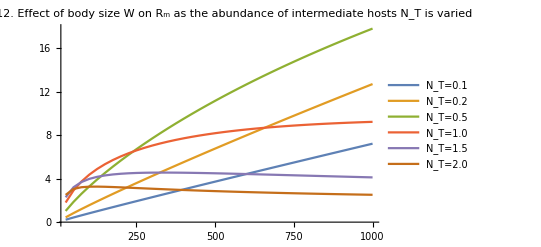
-Graphics-Host mass WGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[Table[{Table[W,{W,25,1000,25}][[i]],InvFitAcrossWNT[[j,i]]},{i,1,40}],{j,1,6}],PlotLegends->{"N_T=0.1","N_T=0.2","N_T=0.5","N_T=1.0","N_T=1.5","N_T=2.0"},PlotLabel->"Fig. S12. Effect of body size W on R_m \nas the abundance of intermediate hosts N_T is varied",PlotRange->All],
{"Host mass W","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

Increasing temperature also has a much more complex effect on R_0: when N_T is large, increasing temperature increases R_0, but when N_T is small, increasing temperature decreases R_0.

Increasing temperature also has a much more complex effect on R_m: when N_T is large, increasing temperature increases R_m (Fig. S13), but when N_T is small, increasing temperature decreases R_m (Fig. S14).

```mathematica
(* Variation in Subscript[R, m] as T varies when Subscript[N, T]=2 *)
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,2,0.01,0.1,0.01],{T,270,310,2}];
```

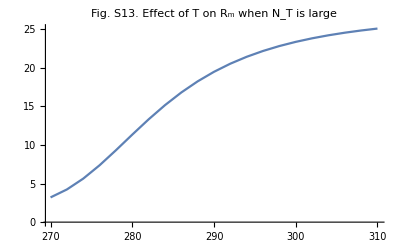
-Graphics-Temperature TGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[{Table[T,{T,270,310,2}][[i]],InvFitAcrossWT[[i]]},{i,1,21}],PlotLabel->"Fig. S13. Effect of T on R_m when N_T is large"],
{"Temperature T","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```

```mathematica
(* Variation in Subscript[R, m] as T varies when Subscript[N, T]=0.1 *)
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,0.1,0.01,0.1,0.01],{T,270,310,2}];
```

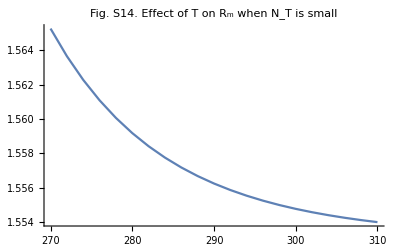
-Graphics-Temperature TGeneralist R_m

```mathematica
Labeled[ListLinePlot[Table[{Table[T,{T,270,310,2}][[i]],InvFitAcrossWT[[i]]},{i,1,21}],PlotLabel->"Fig. S14. Effect of T on R_m when N_T is small"],
{"Temperature T","Generalist R_m"},{Bottom,Left},RotateLabel->True]
```